## Throwing down haplotypes

Some of the figures take a lot of memory, and are best converted to BitMap

## Notes

### Notes on using the notebooks

First, evaluate initialisations in “Longshanks data” and “Selection on pedigrees definitions…”
Sections that need to be evaluated for the following analysis are highlighted.

The definitions should all be in those two notebooks - for the mouse data, and for the simulations, respectively.  However, the distinction is not completely clear, and some definitions combine the two.  One may need to search for function definitions in multiple notebooks.

One possible source of confusion is that I have used several sources of data: 
	- the first frequency data (freqSNP…)
	- the new frequency data (freqSNPNew…)
	- individual data in haploid and diploid genotypes (hapInd, dipInd, freqSNPInd,…)
I have not yet used the “sparsified” data. 
For consistency, the current analysis is all based on the individual data.

### Notes on the method

#### Chromosome lengths

The procedure should be adjusted to the map length of chromosome, so that each simulated block corresponds to an actual segment of the chromosome.

An alternative (which I don’t use) would be to run a set of simulations on the maximum map length, R=1.02, and then subsample these when looking at each chromosome.  That would allow re-use of the simulations, but seems over-complicated.

#### Sampling haplotypes: 5 methods

Sampling haplotypes is not straightforward. One should map directly from the chromosome to the simulation, maintaining the order aIong the genome.  Randomness then comes from how the 2N founder haplotypes are assigned to simulated blocks.  In principle, one could have a different permutation of haplotypes for each interval, without altering the outcome. However, this is complicated, because simulated blocks overlap.  Therefore, I will only permute individuals onto the founder genomes, without breaking up haplotypes.

As explained below, one has four ways of choosing haplotypes:
	- use the phased haplotypes from Frank
	- throw down SNP at the actual frequencies, but in LE (Method→LE in makeHaps)
	- phase diploid individuals by assigning heterozygotes at random (Method→Random in makeHaps)
	- phase diploid individuals by assigning heterozygotes to be all 0 or all 1 (Method→LD in makeHaps)
The last three span a range of possible LD.  The last involves extreme long range LD, but this should not affect the outcome, since the founder genomes will be broken up into fairly small fragments.  A fifth possibility would be to estimate the variance using an estimated pairwise D for each interval separately, without actually assigning SNP.

#### Missing mice

** How to deal with the missing mice?  There were several founder mice that were not genotyped.  I run the simulation using the full pedigree, and so need to seed it with more haplotypes than we have genotypes.  The comparison will be between simulations, and the final allele frequencies. If I use only SNP that were polymorphic in the initial founders, that excludes “impossible” alleles present in F17 but that were missed at the start, but may also lead to  substantial errors for alleles that were initially in multiple copies, but by chance were missed, and genotyped as 1 copy.

Ideally, one would make a best estimate of founder haplotypes from the genotyped subset.  That could be done for the “LE” option, but would not be straightforward - crucially, it cannot be done for reconstructing haplotypes.  There are a few haplotypes (in a few windows, making up a large fraction) that were not sampled in the founders; it is not clear how this influences variability due to SNP sampling.

** A simpler approach is just to resample some haplotypes, from whichever method, and later worry about how much bias this might produce in the SFS.  I implemented this in makeHaps.

Note that the “missing mice” do not actually account for many of the impossible SNP - those seem to be mainly due to calling errors.

#### Allowing for mis-assignment

The main source of error only became apparent from the diploid data: a high rate of mis-assignment of heterozygotes (F~0.45).  So:
	- Take the diploid genotypes of the sampled founding mice
	- Re-sample 2-3 extra genotypes, to represent the missing mice (note that this will not generate any new SNP, and so is not quite accurate)
	- In each interval, shuffle the corresponding SNP, and throw them onto the simulated F17 population
	- Call SNP, thus adding some noise to the observed allele frequencies - store both true and observed frequencies

This last step is straightforward, but does not deal with the main problem - mis-assignment in the founder population, such that heterozygotes are mis-called, lost from the founder sample, and then re-appear in F17 as “impossible” SNP.

#### The procedure

So:
- run the same procedure for the data and for simulations, chromosome by chromosome.
- for each chromosome:
	- run four simulations for neutral, infinitesimal, and infinitesimal with 4 times the genetic variance.
	- start the simulations with the same initial set of selected loci, to maximise replicability, and also, the same set of SNP.
	-  generate a shuffled set of founder haplotypes from the actual diploid data, using the three above methods (LE, Random, LD)
	- for each interval, assign a set of haplotypes, and calculate allele frequencies.
	- calculate the desired statistics (not easy to decide what is needed …)

One could either generate a full simulated population of chromosomes, or more efficiently, just store a simulated set of allele frequencies (if those will be all that is needed).  The initial allele frequencies must necessarily equal those observed, which is not easy if one needs to allow for mis-assignment of heterozygotes

#### Use polymorphic SNP

** We only need to work with SNP that are polymorphic within the population, as long as we don’t deal with replicability issues. However, since the set of polymorphic loci is almost the same for LS1, LS2, we may as well use their union. It is not clear to me why so many more SNP are listed than are actually polymorphic.

** It is important to be clear about what set of SNP is to be used, and how they are to be numbered.  I will use SNP polymorphic anywhere in the sample, including the impossible SNP.

#### What to record? Difficult…

What to record in each interval? We do not need to construct a full set of haplotypes, but rather, just the final and initial allele frequencies - the former varying slightly because of the missing mice.  Thus, we need to record two different transition matrices, as well as perhaps the final allele frequencies along the genome (though that takes a lot of memory).  A more tractable course is to record data from 10kb windows.  An efficient way to do this might be as the transition matrix by window, which is not excessive in memory use (20*200*2500=10^7) integers at most, less using SparseArrays).

This last is not quite right: for each window, we really need the triple {i_0,i_(17,1),i_(17,2)}, which will take much more space. Still, it may be feasible using sparse arrays??  This approach will not work: the sampled frequencies at the start will differ between LS1 and LS2, so one needs a four-dimensional array, which is too large even for the whole chromosome. One has to work with drastically condensed summary statistics.

We need two kinds of statistics: overall F, transition probabilities, Δz in each replicate; and then, measures in (say) 10kb windows.  All these could be calculated from lists of allele frequencies from LS1 and LS2 simulations, which could be stored at most for one chromosome.  So, we do need to find a reduced set of statitsics to calculate for each chromosome in turn.

#### A strategy

First, examine one chromosome in detail, to be sure what statistics are needed; run multiple simulations for this,  throw down SNP, and examine F, ψ[p], replicability of Δz and Δz^2, and pattern across 10kb windows. Then, set this up for all chromosomes.

## Analysis of chromosome 5

### Looking at the data

Below, I look at the data: reproducing (more or less) Frank’s observation of a strong parallel response around 41-42Mb.

I then look at diploid genotypes, trying to find a simple way to derive haplotypes from them, for use in the simulations.

#### Loading data from chromosome 5: 1939083 SNP on 148.7Mb

It takes a few minutes to load individual data for chromosome 5…

```mathematica
Dynamic[{t,r}]
```

```mathematica
Timing[getIndData[5];]
```

{280.207,Null}

#### Some checks

```mathematica
{directoryName[Ind],posFileName[5]}
```

{/Manuscripts/Selection on pedigrees/Longshanks/,beagle_genMap.all.impute.contP0.chr5.diplo.012.pos}

Defines  numSNPInd[c], posSNPInd[c], freqSNPInd[t, r, c], dipInd[t, r, c], hapInd[t, r, c], inds[t, r]. Note that there are no individual data for the control line at the start:

```mathematica
Dimensions/@{posSNPInd[5],freqSNPInd[0,0,5],dipInd[0,0,5],hapInd[0,0,5],inds[0,1]}
```

{{1939083,2},{1939083},{25,1939083},{25,2,1939083},{28}}

The distance between first and last SNP is bigger than the supposed length of the chromosome:

```mathematica
{posSNPInd[5]⟦{1,-1},2⟧,mouseLength[5]}.{-1,1}
```

{1.48713×10^8,146.7}

#### Setting up windows

I use the full list of SNP, which is less efficient than restricting to polymorphic SNP, but leads to less confusion.

```mathematica
dz[r_]:=dz[r]=arcsin[freqSNPInd[17,r,5]]-arcsin[freqSNPInd[0,r,5]];
ps=posSNPInd[5]⟦All,2⟧;
wn=winInd[5,10^4,{0,17},{1,2}];
wn5=winInd[5,10^5,{0,17},{1,2}];
```

This is the histogram of # SNP per window (10kb, 100kb):

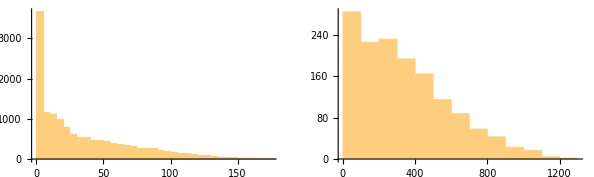

{14314,1453}

```mathematica
GraphicsRow[Histogram[Length/@#]&/@{wn,wn5}]
Length/@{wn,wn5}
```

#### Δz^2 along the genome shows a clear peak at ~41Mb

These are the average Δz^2 per 10kb, 100kb windows, using only windows with >30, 300 SNP (resp.).  Note the strong signal in the  41-42Mbp region highlighted in the MS.

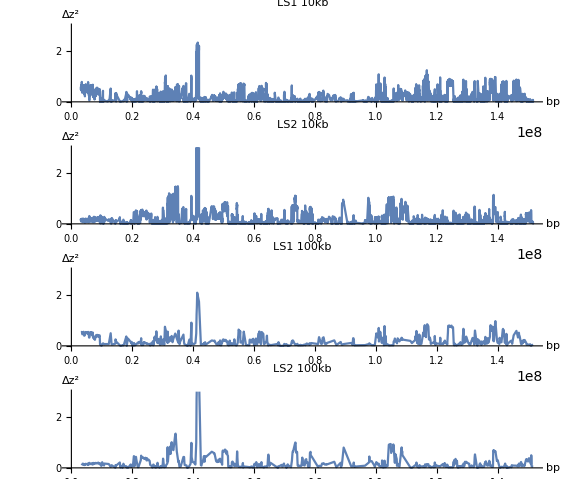

```mathematica
dzz[r_,k_,nt_]:=dzz[r,k,nt]=N[{Mean[posSNPInd[5]⟦#,2⟧],Mean[(dz[r]⟦#⟧)^2]}]&/@Select[winInd[5,10^k,{0,17},{1,2}],Length[#]>nt&];
GraphicsColumn[Flatten[Transpose[Outer[ListLinePlot[dzz[##,If[#2==4,30,300]],AspectRatio->0.2,PlotRange->{Automatic,{0,3}},PlotLabel->"LS"<>ToString[#1]<>If[#2==4," 10kb"," 100kb"],AxesLabel->{"bp","Δz^2"}]&,{1,2},{4,5}]],1]]
```

#### Correlations along the genome seem uninformative

This is the correlation between Δz and Δz^2 (top, bottom) within 100kb windows.  This is not really informative:

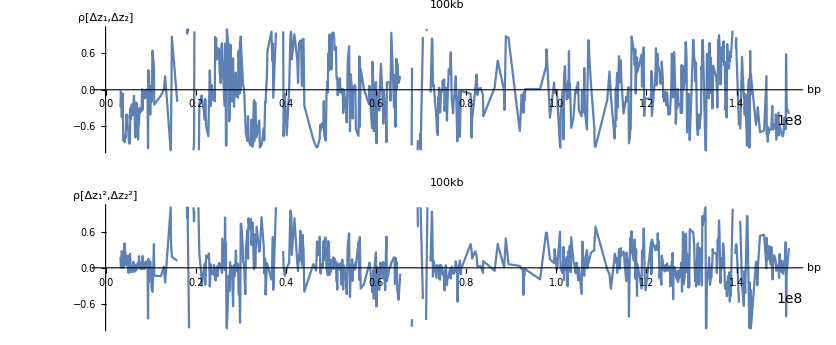

```mathematica
Clear[dzzC,dzzC1];
dzzC[k_,nt_]:=dzzC[k,nt]=N[{Mean[posSNPInd[5]⟦#,2⟧],Correlation[N[dz[1]⟦#⟧]^2,N[dz[2]⟦#⟧]^2]}]&/@Select[winInd[5,10^k,{0,17},{1,2}],Length[#]>nt&];
dzzC1[k_,nt_]:=dzzC1[k,nt]=N[{Mean[posSNPInd[5]⟦#,2⟧],Correlation[N[dz[1]⟦#⟧],N[dz[2]⟦#⟧]]}]&/@Select[winInd[5,10^k,{0,17},{1,2}],Length[#]>nt&];GraphicsColumn[{ListLinePlot[dzzC1[5,300],AspectRatio->0.2,PlotLabel->" 100kb",AxesLabel->{"bp","ρ[Δz_1,Δz_2]"}],
ListLinePlot[dzzC[5,300],AspectRatio->0.2,PlotLabel->" 100kb",AxesLabel->{"bp","ρ[Δz_1^2,Δz_2^2]"}]}]
```

This takes the mean Δz or the mean  Δz^2 (top, bottom) in 10kb windows, and then finds the correlations between these within 1Mb windows (that is, correlating ~100 pairs of numbers).  The pattern looks similar, whether one correlates  Δz or  Δz^2

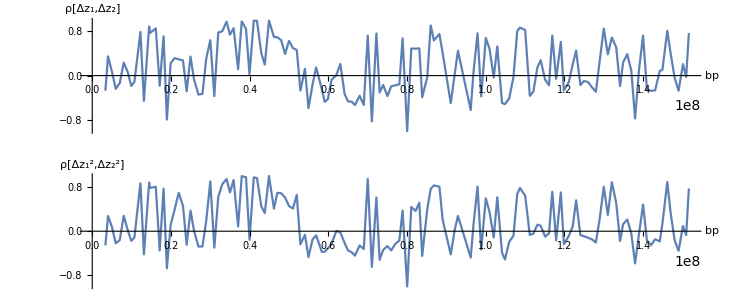

```mathematica
gg[r_]:=GatherBy[dzz[r,4,30],Round[#⟦1⟧/(10^6)]&];
GraphicsColumn[{ListLinePlot[DeleteCases[MapThread[{Mean[#1⟦All,1⟧],Correlation[#1⟦All,2⟧,#2⟦All,2⟧]}&,{gg[1],gg[2]}],{_,Correlation[_,_]}],AspectRatio->0.2,AxesLabel->{"bp","ρ[Δz_1,Δz_2]"}],ListLinePlot[DeleteCases[MapThread[{Mean[#1⟦All,1⟧],Correlation[(#1⟦All,2⟧)^2,(#2⟦All,2⟧)^2]}&,{gg[1],gg[2]}],{_,Correlation[_,_]}],AspectRatio->0.2,AxesLabel->{"bp","ρ[Δz_1^2,Δz_2^2]"}]}]
```

#### The joint distribution of {Δz_1,Δz_2}, {Δz_1^2,Δz_2^2} picks out a strong candidate

This is the joint distribution of {Δz_1,Δz_2} (left) and {Δz_1^2,Δz_2^2} (right).  Colour are graded along the genome (blue…red). The strong outliers are in the 41-42Mb region. It is actually odd that all the SNP go in the same direction in this region - presumably corresponding to the labelling puzzle seen in the individual data. Note the clumping, which presumably reflects haplotype structure common to the two lines.

This is a very large graphic - reduced to BitMap to save memory

```mathematica
dz1[r_]:=dz1[r]=arcsin[freqSNPInd[17,r,5]]-arcsin[freqSNPInd[0,r,5]];
 cd=ColorData["DarkRainbow"];wn30=Select[winInd[5,10^4,{0,17},{1,2}],Length[#]>30&];
wnpk30=Select[wn30,41 10^6<Mean[posSNPInd[5]⟦#,2⟧]<42 10^6&];
xx={cd[Mean[posSNPInd[5]⟦#,2⟧]/(1.6 10^8)],Point[{Mean[dz1[1]⟦#⟧],Mean[dz1[2]⟦#⟧]}]}&/@wn30;
xx2={cd[Mean[posSNPInd[5]⟦#,2⟧]/(1.6 10^8)],Point[{Mean[(dz1[1]⟦#⟧)^2],Mean[(dz1[2]⟦#⟧)^2]}]}&/@wn30;
xxpk={cd[Mean[posSNPInd[5]⟦#,2⟧]/(1.6 10^8)],Point[{Mean[dz1[1]⟦#⟧],Mean[dz1[2]⟦#⟧]}]}&/@wnpk30;
xxpk2={cd[Mean[posSNPInd[5]⟦#,2⟧]/(1.6 10^8)],Point[{Mean[(dz1[1]⟦#⟧)^2],Mean[(dz1[2]⟦#⟧)^2]}]}&/@wnpk30;
GraphicsRow[{Show[Graphics[Join[{PointSize[0.007]},xx,{PointSize[0.012],Red},xxpk]],PlotRange->{{-2.5,2.5},{-2.5,2.5}},AspectRatio->1,Axes->True,AxesLabel->{"Δz_1","Δz_2"}],Show[Graphics[Join[{PointSize[0.007]},xx2,{PointSize[0.012],Red},xxpk2]],PlotRange->{{0,5},{0,5}},AspectRatio->1,Axes->True,AxesLabel->{"Δz_1^2","Δz_2^2"}]}]
```

-Graphics-

These are the correlations for the two diagrams:

```mathematica
{Correlation@@Transpose[N[{Mean[dz[1]⟦#⟧],Mean[dz[2]⟦#⟧]}]&/@wn30],Correlation@@Transpose[N[{Mean[(dz[1]⟦#⟧)^2],Mean[(dz[2]⟦#⟧)^2]}]&/@wn30]}
```

{-0.0213249,0.365073}

#### Examining diploid genotypes

The examples below show that there are runs which should be all heterozygote, but instead are called as random genotypes.  One procedure, then, is to assign such runs as pure heterozygote.  Then, the minimum LD procedure will come put the same - random assignment of 0 or 1 along the run. The maximum LD procedure will be different in an important way, however: haplotypes will be correctly assigned as long runs of 0 or 1, rather than incorrectly, as a mosaic of 0 & 1.

By eye, one can easily see where there is a “mosaic” pattern that indicates presence of a run of heterozygotes.  However, it is not so easy to pick that out. Possibly:
	- restrict to loci polymorphic in LS1, LS2 founders, and combine LS1 and LS2 for the analysis
	- For a given region, define regions that are mainly homozygous as such, and regions with {0,1,2} as heterozygous
	- other regions remain undefined, unless they can be constructed from homozygotes
	- expand core regions until they become heterogeneous.

I have not pursued this further, since although I can see an algorithm for rescoring heterozygous runs, this is not so easy to implement, and may be superceded by better data.

Looking more at the diplotypes does make yet more prominent the puzzle that there seem to be only two haplotypes across much of the genome, and that these are labelled (close to) all 0 and all 1.  Necessarily, these core haplotypes are precisely complementary: if there are only two haplotypes, that must be the case.  It is surprising that they are precisely complementary, at least in some regions, suggesting that homozygotes are scored accurately.

#### Looking at some examples

I examine the 41-42Mb region, considering only the 2979 SNP polymorphic on LS1 or LS2 founders, and sorting by net frequency. Both lines are shown together.

```mathematica
pl=polLoci[0,{1,2},5];
locs=Select[Range[numSNPInd[5]],(41 10^6<posSNPInd[5]⟦#,2⟧<42 10^6)&];Length/@{pl,locs,Intersection[pl,locs]}
```

{464338,13288,2979}

One can see clear blocks of different kinds.  Note first that there are many homozygous black, and one homozygous white; thus, mosaic regions should really be heterozygous.  A taxonomy:
	- white with some grey - correct assignment of a run of heterozygous loci; 2/3 along, there is a black homozygote in such a region.
	- the majority blocks are a mosaic of random {0,1,2}, which should be a run of heterozygotes.

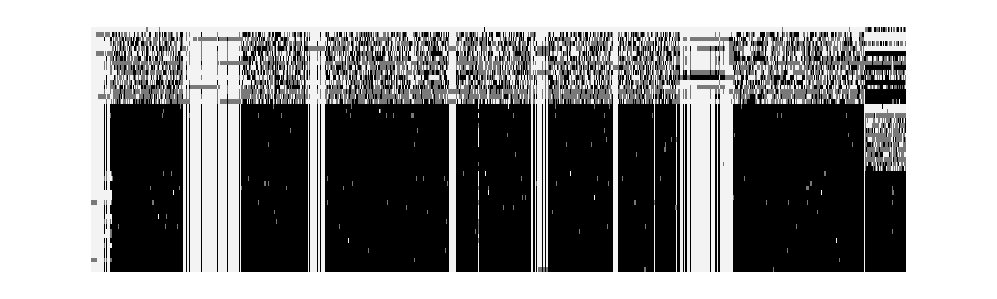

```mathematica
ArrayPlot[0.1+SortBy[Join[dipInd[0,1,5],dipInd[0,2,5]]⟦All,Intersection[pl,locs]⟧,Total],AspectRatio->0.3]
```

In the 51-52Mb region, there are many more polymorphic SNP  (6989):

```mathematica
locs2=Select[Range[numSNPInd[5]],(51 10^6<posSNPInd[5]⟦#,2⟧<52 10^6)&];
Length/@{pl,locs2,Intersection[pl,locs2]}
```

{464338,12280,6989}

```mathematica
ArrayPlot[0.1+SortBy[Join[dipInd[0,1,5],dipInd[0,2,5]]⟦All,Intersection[pl,locs2]⟧,Total],AspectRatio->0.3]
```

-Graphics-

This is an inset into such a region:

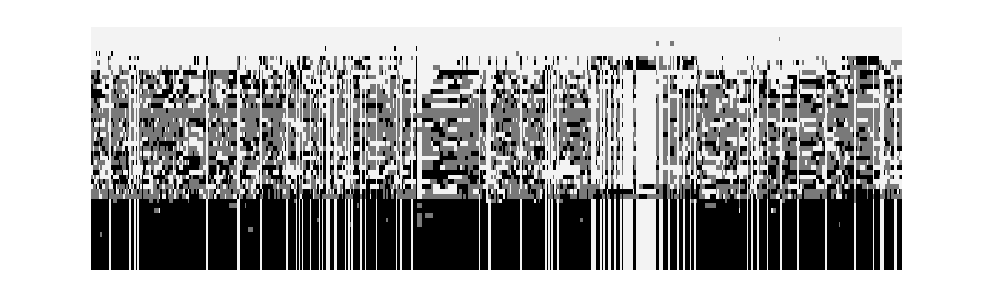

```mathematica
ArrayPlot[0.1+SortBy[Join[dipInd[0,1,5],dipInd[0,2,5]]⟦All,Intersection[pl,locs2⟦1;;1000⟧]⟧,Total],AspectRatio->0.3]
```

#### Algorithm for assigning heterozygous runs (in progress)

This is unfinished: a rough algorithm is clear, but it is not so easy to code..

```mathematica
pl=polLoci[0,{1,2},5];
```

```mathematica
dd=Join[dipInd[0,1,5],dipInd[0,2,5]];Dimensions[dd]
```

{51,1939083}

This 2.1Mb region is somewhat homogeneous, but contains multiple somewhat distinct subregions:

```mathematica
locs2=Select[Range[numSNPInd[5]],(49.5 10^6<posSNPInd[5]⟦#,2⟧<51.6 10^6)&];
ArrayPlot[0.1+SortBy[dd⟦All,Intersection[pl,locs2]⟧,Total],AspectRatio->0.2]
Length/@{pl,locs2,Intersection[pl,locs2]}
```

-Graphics-

{464338,27292,15427}

This is a smaller and vaguely homogeneous sub-region.  I would simply reassign the mosaic region to be runs of heterozygotes.

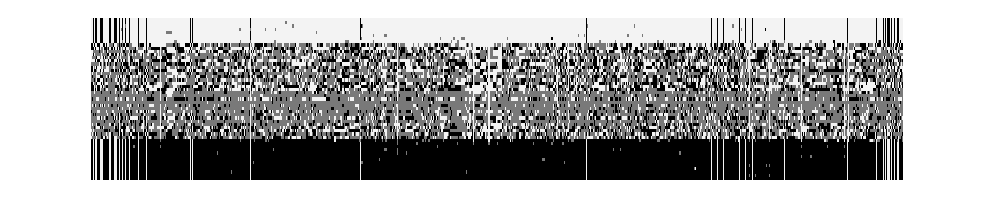

{464338,2210,1395}

```mathematica
locs2=Select[Range[numSNPInd[5]],(50. 10^6<posSNPInd[5]⟦#,2⟧<50.2 10^6)&];
ArrayPlot[0.1+SortBy[dd⟦All,Intersection[pl,locs2]⟧,Total],AspectRatio->0.2]
Length/@{pl,locs2,Intersection[pl,locs2]}
```

There are 1395 SNP in this region

```mathematica
ipl=Intersection[pl,locs2];Length[ipl]
```

1395

This gives the # of the three genotypes that each individual has, sorted by # of heterozygotes.  There is a very odd pattern: some individuals are precise mirror images. There is a sharp break between those with ≤81 heterozygotes, and those with >404, and wide variation in the # of heterozygotes above that threshold. I guess that the spread reflects coverage: all are heterozygous, but the fraction mis-assigned varies with coverage (testable!).

```mathematica
cc=BinCounts[#,{0,3}]&/@dd⟦All,ipl⟧;
scc=Sort[cc,#1⟦2⟧<#2⟦2⟧&]
```

{{1334,0,61},{61,0,1334},{62,3,1330},{61,4,1330},{1330,4,61},{61,4,1330},{61,6,1328},{61,6,1328},{61,7,1327},{61,8,1326},{61,8,1326},{1323,10,62},{61,10,1324},{1322,11,62},{61,12,1322},{1322,12,61},{61,15,1319},{1318,16,61},{1315,17,63},{1269,57,69},{86,81,1228},{558,404,433},{511,424,460},{498,427,470},{488,455,452},{482,468,445},{473,491,431},{497,520,378},{509,525,361},{425,583,387},{381,587,427},{416,612,367},{371,623,401},{378,627,390},{405,635,355},{307,663,425},{348,710,337},{298,715,382},{293,784,318},{329,791,275},{316,801,278},{296,854,245},{244,905,246},{191,1008,196},{213,1010,172},{178,1045,172},{166,1085,144},{143,1088,164},{109,1182,104},{75,1262,58},{16,1372,7}}

These are the positions of these individuals:

```mathematica
Flatten[Position[cc,#]]&/@scc
```

{{18},{4},{21},{12,41},{22},{12,41},{5,26},{5,26},{43},{29,49},{29,49},{45},{30},{31},{48},{17},{38},{28},{39},{8},{2},{13},{25},{14},{50},{9},{7},{20},{40},{33},{6},{32},{35},{51},{34},{19},{11},{23},{44},{10},{36},{16},{46},{42},{37},{27},{1},{15},{3},{47},{24}}

Left: histogram of the # of heterozygotes; Right: the histogram of Hamming distance between all pairs. There are 87 pairs that are closer than 50, and 123 pairs that are within 50 of being as far apart as possible:

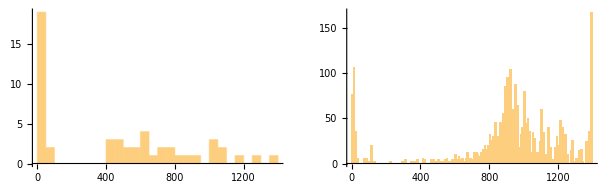

```mathematica
dm=Outer[HammingDistance,dd⟦All,ipl⟧,dd⟦All,ipl⟧,1];
GraphicsRow[{Histogram[cc⟦All,2⟧,20],Histogram[Flatten[dm],100]}]
```

```mathematica
{Length/@{Select[Flatten[dm],0<#<50&],Select[Flatten[dm],1345<#&]}/2,51 50/2}
```

{{87,123},1275}

```mathematica
Sort[Tally[Flatten[dm]]]
```

{{0,51},{4,10},{6,4},{7,2},{8,10},{10,14},{11,6},{12,20},{13,6},{14,14},{15,6},{16,20},{17,4},{18,6},{19,10},{20,4},{21,6},{22,4},{23,6},{24,4},{25,2},{27,2},{28,4},{29,4},{31,2},{32,2},{35,2},{72,2},{75,2},{76,2},{80,2},{84,2},{86,2},{91,2},{107,2},{111,4},{113,2},{114,4},{115,4},{117,4},{118,2},{120,2},{139,2},{221,2},{292,2},{314,2},{315,2},{349,2},{354,2},{368,2},{386,2},{387,2},{410,2},{418,2},{419,2},{420,2},{423,2},{463,2},{468,2},{472,2},{476,2},{487,2},{490,2},{500,2},{503,2},{517,2},{525,2},{539,2},{545,4},{554,2},{555,2},{558,2},{561,2},{570,2},{584,2},{588,2},{603,2},{605,4},{606,2},{609,2},{614,2},{615,2},{621,2},{626,4},{629,2},{632,2},{635,2},{646,2},{647,4},{650,2},{661,2},{665,2},{669,2},{671,2},{674,2},{675,2},{679,6},{684,2},{688,4},{691,4},{696,2},{705,2},{708,2},{710,2},{712,2},{713,2},{714,2},{715,2},{717,2},{721,2},{723,2},{724,2},{725,4},{727,2},{730,4},{735,2},{737,2},{739,2},{740,2},{741,2},{744,2},{746,2},{750,2},{752,2},{753,2},{754,2},{755,2},{756,2},{760,4},{761,2},{762,2},{764,2},{768,2},{769,4},{770,2},{771,2},{774,4},{775,2},{776,4},{777,2},{778,4},{780,6},{781,2},{785,4},{787,2},{789,2},{790,6},{792,4},{793,2},{794,2},{797,4},{798,2},{800,2},{801,8},{802,2},{803,4},{804,2},{805,2},{806,4},{807,2},{808,2},{809,4},{810,4},{811,4},{812,2},{815,4},{817,6},{818,2},{819,4},{820,2},{822,4},{824,4},{825,4},{826,2},{827,4},{828,6},{829,4},{830,12},{832,2},{834,10},{836,8},{837,4},{838,4},{839,6},{840,2},{843,6},{844,2},{845,4},{846,4},{851,2},{852,6},{853,2},{855,2},{857,4},{858,6},{859,8},{860,4},{861,6},{862,2},{863,2},{864,8},{865,2},{866,6},{867,4},{868,4},{869,8},{870,2},{871,6},{872,10},{873,4},{874,4},{876,8},{878,6},{879,6},{880,2},{881,6},{882,6},{883,2},{884,2},{885,4},{886,4},{887,8},{888,12},{889,10},{890,10},{891,4},{892,10},{893,4},{894,14},{895,4},{896,12},{897,10},{898,8},{899,10},{900,6},{901,12},{902,10},{903,8},{904,10},{905,2},{906,6},{907,12},{908,16},{909,14},{910,8},{911,12},{912,6},{913,2},{914,8},{915,14},{916,6},{917,6},{918,6},{919,6},{920,10},{921,16},{922,14},{923,16},{924,6},{925,12},{926,8},{927,2},{928,14},{929,6},{930,8},{931,12},{932,6},{934,6},{935,8},{936,6},{937,4},{938,2},{939,8},{940,8},{942,2},{943,10},{945,8},{946,6},{947,8},{948,2},{949,4},{950,18},{951,10},{952,10},{953,12},{954,6},{955,6},{956,8},{957,8},{958,2},{959,8},{960,4},{961,10},{962,14},{963,4},{964,2},{965,8},{966,8},{967,6},{968,2},{969,6},{971,6},{975,2},{976,4},{977,4},{979,2},{980,2},{981,2},{983,4},{984,2},{985,2},{986,8},{987,4},{988,2},{989,6},{990,6},{991,6},{993,2},{994,2},{995,4},{996,2},{997,6},{998,6},{999,6},{1000,6},{1001,6},{1002,4},{1003,8},{1004,12},{1005,2},{1006,12},{1007,6},{1008,16},{1009,8},{1010,4},{1011,2},{1012,2},{1013,2},{1014,6},{1015,10},{1016,2},{1017,2},{1018,8},{1019,6},{1020,10},{1021,16},{1022,4},{1023,6},{1024,6},{1025,4},{1029,4},{1030,4},{1031,10},{1032,4},{1033,2},{1034,10},{1035,2},{1036,2},{1037,2},{1041,4},{1047,2},{1048,2},{1049,4},{1050,10},{1051,2},{1052,10},{1053,2},{1054,2},{1055,4},{1057,2},{1058,2},{1061,2},{1062,4},{1063,2},{1064,4},{1065,6},{1066,2},{1067,4},{1068,2},{1069,2},{1070,2},{1071,2},{1073,2},{1075,4},{1078,2},{1083,2},{1084,2},{1087,6},{1089,2},{1090,4},{1091,2},{1093,2},{1094,2},{1095,2},{1096,6},{1099,6},{1101,4},{1102,4},{1103,10},{1104,4},{1105,6},{1106,8},{1107,2},{1108,12},{1109,10},{1110,6},{1111,6},{1112,6},{1113,6},{1114,4},{1115,4},{1117,2},{1124,2},{1132,2},{1135,2},{1138,2},{1139,4},{1141,6},{1142,2},{1143,8},{1144,2},{1145,4},{1146,6},{1147,8},{1148,2},{1149,2},{1150,6},{1151,4},{1152,4},{1153,2},{1158,2},{1163,2},{1167,2},{1174,2},{1176,2},{1180,2},{1182,4},{1183,2},{1184,4},{1186,2},{1188,2},{1189,2},{1190,4},{1191,6},{1193,4},{1194,6},{1195,2},{1196,2},{1197,4},{1198,2},{1200,2},{1202,4},{1203,2},{1204,2},{1205,2},{1206,2},{1207,4},{1209,2},{1210,2},{1211,4},{1212,12},{1213,4},{1214,2},{1216,6},{1217,4},{1218,6},{1219,8},{1220,2},{1221,2},{1222,8},{1223,8},{1224,8},{1225,2},{1226,6},{1227,4},{1230,2},{1240,2},{1242,6},{1243,4},{1244,2},{1245,6},{1246,2},{1247,8},{1249,2},{1250,2},{1252,2},{1253,4},{1256,2},{1270,2},{1272,4},{1275,2},{1277,2},{1278,2},{1279,2},{1282,2},{1283,8},{1284,6},{1286,2},{1287,8},{1290,2},{1306,4},{1308,2},{1313,4},{1319,2},{1321,2},{1323,2},{1327,4},{1328,4},{1329,2},{1330,6},{1331,4},{1332,2},{1334,4},{1348,2},{1360,2},{1362,4},{1363,6},{1364,2},{1365,4},{1367,2},{1368,2},{1369,2},{1375,2},{1376,2},{1377,2},{1378,4},{1379,6},{1380,22},{1381,2},{1382,4},{1384,4},{1385,2},{1388,2},{1391,4},{1392,4},{1393,42},{1394,52},{1395,66}}

Now, look at another example, which is more troublesome. At the right 2/3, there is a somewhat heterozygous region embedded in the run of black homozygotes; and over most of the length, there are (roughly) two slightly different homozygous diplotypes (top rows).

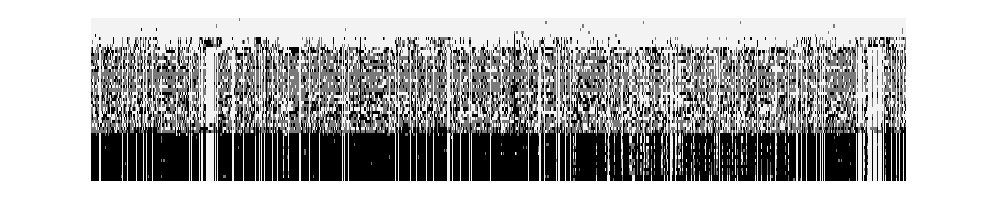

{464338,3887,2458}

```mathematica
locs3=Select[Range[numSNPInd[5]],(51. 10^6<posSNPInd[5]⟦#,2⟧<51.3 10^6)&];
ArrayPlot[0.1+SortBy[dd⟦All,Intersection[pl,locs3]⟧,Total],AspectRatio->0.2]
Length/@{pl,locs3,Intersection[pl,locs3]}
```

```mathematica
ipl3=Intersection[pl,locs3];Length[ipl3]
```

2458

There is a break at about 500 heterozygotes; the homozygous peaks are not so clear, and we do not see precise complementarity.

```mathematica
cc3=BinCounts[#,{0,3}]&/@dd⟦All,ipl3⟧;
scc3=Sort[cc3,#1⟦2⟧<#2⟦2⟧&]
```

{{2457,1,0},{2446,11,1},{2444,11,3},{423,15,2020},{2442,16,0},{2429,17,12},{411,20,2027},{416,22,2020},{2430,27,1},{385,29,2044},{382,47,2029},{373,81,2004},{369,83,2006},{382,87,1989},{376,93,1989},{359,129,1970},{355,142,1961},{349,143,1966},{325,167,1966},{334,172,1952},{393,219,1846},{1975,245,238},{1957,289,212},{1884,375,199},{1115,606,737},{1111,634,713},{1189,637,632},{1157,643,658},{1064,712,682},{1084,748,626},{1026,791,641},{999,820,639},{1049,834,575},{995,865,598},{1043,870,545},{968,873,617},{986,927,545},{945,979,534},{631,1030,797},{873,1102,483},{882,1110,466},{772,1138,548},{829,1183,446},{710,1386,362},{719,1450,289},{738,1468,252},{339,1507,612},{692,1546,220},{662,1547,249},{523,1823,112},{451,1987,20}}

```mathematica
Flatten[Position[cc3,#]]&/@scc3
```

{{22},{31},{18},{21},{17},{39},{48},{26},{28},{12},{41},{4},{49},{5},{43},{36},{38},{29},{3},{30},{2},{8},{45},{35},{50},{13},{14},{25},{7},{9},{6},{20},{40},{19},{32},{33},{51},{11},{23},{16},{44},{34},{10},{46},{42},{15},{1},{37},{27},{47},{24}}

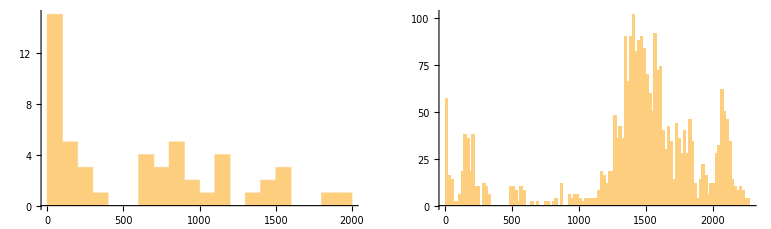

```mathematica
dm3=Outer[HammingDistance,dd⟦All,ipl3⟧,dd⟦All,ipl3⟧,1];
GraphicsRow[{Histogram[cc3⟦All,2⟧,20],Histogram[Flatten[dm3],100]}]
```

### Understanding the effects of calling errors

#### More thoughts on the missing mice & on SNP calling errors

Examining the diploid genotypes suggests that in most individuals, heterozygotes are mis-called randomly as homozygotes.  This would not disturb the bulk allele frequencies (in expectation), but would explain the substantial heterozygote deficit, and would lead to “impossible” SNP, if rare heterozygotes were mis-called as the common homozygote.

The other cause of impossible SNP - missing founder mice - seems unable to produce as many errors as we see. That can be checked (at least roughly) by removing  founder mice, and asking how that affects the # of impossible SNP.

#### What to do?

If, as it seems, half the heterozygotes are mis-called as homozygotes, the analysis needs to be radically changed.  The allele frequency analysis may not need so much adjustment, but it becomes even less clear how to deal with haplotype structure.

- In order to estimate the heterozygote deficit, one needs to work with diploid data; F can be estimated as a function of coverage.
- Mis-assignment does not (much) alter the conditional allele frequency spectrum, but does increase the noise.
- There is an important effect at the edges: the initial frequency is mis-estimated, and that does have to be allowed for in the predicted allele frequency distributions.
- Ultimately, we need a way to throw haplotypes onto the simulations.
- Before, I set up options for constructing haplotypes from diploid data:
	- LE, using observed SNP frequencies
	- minimum LD, assigning heterozygotes randomly
	- maximum LD, assigning heterozygotes as all 0 or all 1
For each case, I construct a complete set of haplotypes; from these, I sub-sample the initial numbers, allowing for both missing mice and for mis-allocation of heterozygotes.  These simulated data can be compared with the initial configurations, and I can use all SNP that are polymorphic in LS1, LS2 at beginning or end.  The final frequencies can be analysed simply as frequencies, since sampling was complete, and since mis-assignment does not (by assumption) alter allele frequencies.
- How does this account for mis-assignment of heterozygotes?
	- The LE option should be correct, at least away from the edges.  If one threw down SNP with the observed frequency distribution onto the source, and then subsampled & re-assigned genotypes, one could check against the observed configurations.  One perhaps doesn’t need an exact fit, since one is looking for differences along the genome.
	- The minimum LD option may now be quite misleading, since homozygotes are often incorrect.
	- The maximum LD option now essentially requires phasing. Suppose that in an interval, there are long runs of homozygotes. These identify the common haplotypes, and one could re-label to define these as the ‘local’ haplotypes.  Then, one identifies heterozygotes as being more or less likely to be combinations of these haplotypes, allowing here for misassignment. 
	- This could be done using  the founders, but one would need to decide whether to use LS1, LS2 separately, or together.

For this to be convincing, one really needs to devise a local phasing algorithm.

#### Including sampling error and mis-assignment in the conditional probability

Suppose that one observes {i_1,i_2} at the beginning, and then {k_1,k_2} at the end - or k_* at the end (just looking at total #).  This probability is:

Pr[k_17|{i_1,i_2}]=C∑_k_0 Pr[i_17^*|k_17]Pr[k_17|k_0]Pr[{i_1,i_2}|k_0]

where C is a normalisation.  This includes both the missing mice, mis-allocation of heterozygotes at the start, and mis-allocation at the end.

Actually, this approach is not so helpful, because the transition probability needs to be found by simulation, and so one comes back to the problem of how to simulate the whole process of (imperfectly) observing SNP.

#### Basic numbers

There are 28 individuals in the LS1 and LS2 founders, but only 2/25 were sampled

```mathematica
{Dimensions[pedigree[#]⟦1⟧],Length[dipInd[0,#,5]]}&/@{1,2}
```

{{{28,28},26},{{28,28},25}}

These are the numbers of loci polymorphic in one or other of LS1, LS2 at beginning and end, and then the # polymorphic at the beginning & not the end, and vice versa; the last entry is in principle impossible, but is a combination of scoring error and missing mice.

```mathematica
Length/@{polLoci[0,{1,2},5],polLoci[17,{1,2},5],Complement[polLoci[0,{1,2},5],polLoci[17,{1,2},5]],Complement[polLoci[17,{1,2},5],polLoci[0,{1,2},5]]}
```

{464338,448237,42077,25976}

#### i_17 vs i_0

This gives the final # of copies (out of 64) in LS1, as a function of the initial frequency.  Note that i) there are some “impossible” alleles (0.0005625, 0.00055625 at the two extremes), and ii) there are substantial fluctuations around linearity

```mathematica
n=2Length[dipInd[17,1,5]];
ss=Table[pl=pickLoci[k,0,1,5];
tt=Tally[n freqSNPInd[17,1,5]⟦pl⟧]//Sort;
{Total[tt⟦All,2⟧],(tt⟦All,1⟧.tt⟦All,2⟧)/Total[tt⟦All,2⟧]//N},{k,0,52}]
```

{{1460899,0.0363256},{36380,1.66297},{26229,3.10973},{17726,4.55015},{15205,5.4021},{9384,7.40079},{9518,9.25268},{7816,9.21034},{8302,7.76391},{9760,6.65748},{11214,5.75004},{12676,5.82195},{11509,7.25337},{10638,7.85289},{9568,9.70036},{8956,13.1606},{8171,16.385},{7706,20.1799},{8382,21.4297},{7136,24.0465},{6452,25.8435},{5813,27.545},{5707,28.8328},{5220,31.0067},{5182,33.312},{5429,36.0304},{6091,37.4845},{6916,39.0191},{7616,39.8967},{7750,40.4587},{8113,40.8041},{8034,40.5617},{8963,40.0476},{9706,39.4654},{9393,39.8777},{8652,39.5157},{6918,41.0853},{5820,42.489},{5192,44.1262},{4845,45.6625},{6664,41.6002},{6720,49.7744},{5680,50.6143},{5708,51.3336},{4828,51.7728},{4083,52.5205},{3491,54.0862},{3131,55.9757},{3397,58.1816},{3296,59.8319},{3960,61.3101},{2356,62.1146},{50782,63.9644}}

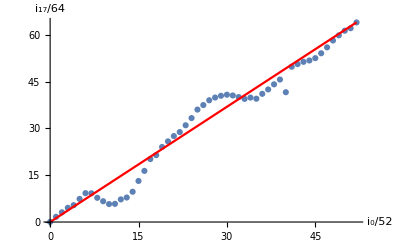

```mathematica
Show[ListPlot[Transpose[{Range[0,52],ss⟦All,2⟧}]],Plot[64/52 k,{k,0,52},PlotStyle->Red],AxesLabel->{"i_0/52","i_17/64"}]
```

#### Tabulating all possible diploid configurations in the founders:

There are only a few ways of achieving low counts. For example, with 2 copies, about 71% of cases are two heterozygotes, and 29% are homozygotes. 
1 | {1,1} |   |  
  | 36380 |   |  
2 | {1,2} | {2,1} |  
  | 18840 | 7389 |  
3 | {1,3} | {2,1},{1,1} |  
  | 9498 | 8228 |  
4 | {1,4} | {2,1},{1,2} | {2,2}
  | 6072 | 7554 | 1579

This tabulates the numbers of all possible configurations of {i_1,i_2}:

```mathematica
tt=dipConfigs[0,1,5]
```

{{{0,0},1460899},{{0,1},7389},{{0,2},1579},{{0,3},427},{{0,4},188},{{0,5},129},{{0,6},62},{{0,7},37},{{0,8},24},{{0,9},18},{{0,10},28},{{0,11},33},{{0,12},29},{{0,13},19},{{0,14},33},{{0,15},13},{{0,16},40},{{0,17},67},{{0,18},41},{{0,19},40},{{0,20},103},{{0,21},82},{{0,22},98},{{0,23},166},{{0,24},269},{{0,25},682},{{0,26},50782},{{1,0},36380},{{1,1},8228},{{1,2},2390},{{1,3},867},{{1,4},464},{{1,5},318},{{1,6},203},{{1,7},172},{{1,8},119},{{1,9},100},{{1,10},109},{{1,11},85},{{1,12},78},{{1,13},84},{{1,14},72},{{1,15},135},{{1,16},203},{{1,17},198},{{1,18},233},{{1,19},287},{{1,20},294},{{1,21},425},{{1,22},408},{{1,23},675},{{1,24},1655},{{1,25},2356},{{2,0},18840},{{2,1},7554},{{2,2},3022},{{2,3},1473},{{2,4},938},{{2,5},699},{{2,6},518},{{2,7},503},{{2,8},349},{{2,9},272},{{2,10},249},{{2,11},243},{{2,12},161},{{2,13},241},{{2,14},309},{{2,15},563},{{2,16},673},{{2,17},613},{{2,18},612},{{2,19},2169},{{2,20},867},{{2,21},911},{{2,22},1115},{{2,23},1831},{{2,24},3278},{{3,0},9498},{{3,1},5204},{{3,2},2998},{{3,3},2150},{{3,4},2415},{{3,5},1384},{{3,6},1285},{{3,7},1019},{{3,8},858},{{3,9},593},{{3,10},462},{{3,11},420},{{3,12},435},{{3,13},545},{{3,14},975},{{3,15},1695},{{3,16},1579},{{3,17},1104},{{3,18},1190},{{3,19},2601},{{3,20},2066},{{3,21},1761},{{3,22},1749},{{3,23},1641},{{4,0},6072},{{4,1},4805},{{4,2},2963},{{4,3},3164},{{4,4},2798},{{4,5},2358},{{4,6},2197},{{4,7},1751},{{4,8},1362},{{4,9},1040},{{4,10},922},{{4,11},871},{{4,12},1177},{{4,13},1450},{{4,14},2204},{{4,15},3247},{{4,16},2026},{{4,17},1653},{{4,18},1941},{{4,19},2443},{{4,20},2434},{{4,21},1708},{{4,22},1297},{{5,0},1790},{{5,1},3188},{{5,2},4011},{{5,3},4795},{{5,4},3902},{{5,5},3322},{{5,6},2807},{{5,7},2392},{{5,8},1741},{{5,9},1633},{{5,10},1353},{{5,11},1811},{{5,12},2000},{{5,13},2319},{{5,14},3102},{{5,15},3126},{{5,16},2012},{{5,17},1845},{{5,18},2505},{{5,19},2325},{{5,20},1627},{{5,21},707},{{6,0},1264},{{6,1},3290},{{6,2},4834},{{6,3},4769},{{6,4},3885},{{6,5},3290},{{6,6},3045},{{6,7},2367},{{6,8},2164},{{6,9},1666},{{6,10},2027},{{6,11},2567},{{6,12},2786},{{6,13},2968},{{6,14},3034},{{6,15},2376},{{6,16},1760},{{6,17},1766},{{6,18},1800},{{6,19},1237},{{6,20},502},{{7,0},763},{{7,1},2645},{{7,2},4002},{{7,3},3777},{{7,4},2939},{{7,5},2502},{{7,6},2356},{{7,7},2020},{{7,8},1770},{{7,9},1934},{{7,10},2386},{{7,11},2749},{{7,12},2745},{{7,13},3057},{{7,14},2341},{{7,15},1764},{{7,16},1195},{{7,17},1139},{{7,18},834},{{7,19},287},{{8,0},388},{{8,1},2028},{{8,2},2786},{{8,3},2315},{{8,4},1665},{{8,5},2519},{{8,6},1672},{{8,7},1490},{{8,8},1527},{{8,9},1931},{{8,10},2238},{{8,11},2350},{{8,12},2214},{{8,13},1677},{{8,14},1457},{{8,15},919},{{8,16},599},{{8,17},474},{{8,18},148},{{9,0},490},{{9,1},1105},{{9,2},1224},{{9,3},1092},{{9,4},993},{{9,5},1142},{{9,6},1033},{{9,7},942},{{9,8},1213},{{9,9},1583},{{9,10},1692},{{9,11},1409},{{9,12},1319},{{9,13},1248},{{9,14},584},{{9,15},305},{{9,16},174},{{9,17},58},{{10,0},121},{{10,1},327},{{10,2},442},{{10,3},428},{{10,4},537},{{10,5},581},{{10,6},531},{{10,7},636},{{10,8},877},{{10,9},1061},{{10,10},996},{{10,11},858},{{10,12},513},{{10,13},346},{{10,14},192},{{10,15},86},{{10,16},14},{{11,0},41},{{11,1},148},{{11,2},135},{{11,3},220},{{11,4},260},{{11,5},294},{{11,6},264},{{11,7},374},{{11,8},526},{{11,9},573},{{11,10},402},{{11,11},318},{{11,12},140},{{11,13},122},{{11,14},23},{{11,15},7},{{12,0},68},{{12,1},13},{{12,2},61},{{12,3},160},{{12,4},145},{{12,5},192},{{12,6},146},{{12,7},183},{{12,8},273},{{12,9},193},{{12,10},108},{{12,11},177},{{12,12},59},{{12,13},16},{{13,1},10},{{13,2},46},{{13,3},28},{{13,4},21},{{13,5},57},{{13,6},51},{{13,7},88},{{13,8},108},{{13,9},48},{{13,10},10},{{13,11},19},{{13,12},1},{{14,1},3},{{14,2},3},{{14,3},11},{{14,4},7},{{14,5},11},{{14,6},22},{{14,7},25},{{14,8},16},{{14,9},8},{{14,10},5},{{15,0},1},{{15,3},1},{{15,4},7},{{15,5},6},{{15,6},3},{{15,7},11},{{15,8},1},{{15,9},2},{{16,2},14},{{16,3},1},{{16,4},1},{{16,6},1},{{17,9},1},{{18,3},1},{{19,1},1}}

which may take a while.

#### Estimating F=0.451 for LS1 founders

This is the raw frequency distribution in the founders:

```mathematica
fd=BinCounts[52freqSNPInd[0,1,5],{0,53}]
```

{1460899,36380,26229,17726,15205,9384,9518,7816,8302,9760,11214,12676,11509,10638,9568,8956,8171,7706,8382,7136,6452,5813,5707,5220,5182,5429,6091,6916,7616,7750,8113,8034,8963,9706,9393,8652,6918,5820,5192,4845,6664,6720,5680,5708,4828,4083,3491,3131,3397,3296,3960,2356,50782}

This is the log likelihood of F, assuming the raw frequency distribution.  Because there are so many SNP, the log(L) is enormous; this is misleading, since the SNP are highly correlated.  F̂=0.451:

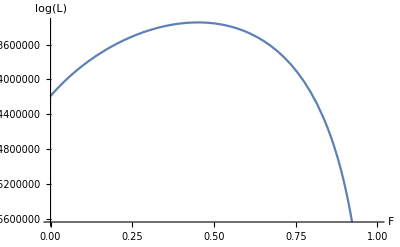

{-3.34532×10^6,{F→0.450898}}

```mathematica
tfd=Total[fd]//N;
mn=Total[tt/.{{i1_,i2_},k_}:> k Log[1/tfd∑_(j=0)^52 fd⟦j+1⟧ prDip[{i1,i2},26,j/52,F]]];
Plot[mn,{F,0,1},AxesLabel->{"F","log(L)"}]
FindMaximum[mn,{F,0.75}]
```

This gives the same result. It takes a few minutes, because it tallies the diploid configurations across all loci:

```mathematica
estF[0,1,5]
```

{-3.34532×10^6,{F→0.450898}}

#### Estimating F, given i_0, assuming a multinomial distribution

The probability of seeing {i_1,i_2} is multinomial:

P[i_1,i_2]=𝔼[(n
i_1,i_2,n-i_1-i_2)u_0^n(u_1/u_0)^i_1(u_2/u_0)^i_2]
u_0=q^2+pqF, u_1=2pq(1-F), u_2=p^2+pqF

where the expectation  is over the distribution of p.  One can estimate the distribution of p directly, and given that, estimate F, and predict the distribution of F, conditional on p̂. The relative proportion of heterozygotes, conditional on observing  i_1+2 i_2=j copies is:

∑_(i_2=0)^(j/2) P[i_1=j-2 i_2,i_2]i_1/(j(1-j/(2n)))

Assuming this estimate of F̂=0.451, and the raw frequency distribution, this is the estimate of F, conditional on the observed # of copies:

```mathematica
ftt=Table[1/(j(1-j/52))((fd⟦2;;-2⟧/Total[fd⟦2;;-2⟧]).Table[(∑_(i2=0)^Quotient[j,2] prDip[{j-2i2,i2},26,i/52,0.451](j-2i2))/(∑_(i2=0)^Quotient[j,2] prDip[{j-2i2,i2},26,i/52,0.451]),{i,1,51}]),{j,1,51}]
```

{1.01961,0.794634,0.739701,0.67402,0.641636,0.606373,0.584664,0.561938,0.546381,0.530414,0.518843,0.507093,0.498321,0.489466,0.482786,0.476063,0.471029,0.46597,0.462293,0.458598,0.456089,0.453565,0.452106,0.450633,0.450158,0.449669,0.450158,0.450633,0.452106,0.453565,0.456089,0.458598,0.462293,0.46597,0.471029,0.476063,0.482786,0.489466,0.498321,0.507093,0.518843,0.530414,0.546381,0.561938,0.584664,0.606373,0.641636,0.67402,0.739701,0.794634,1.01961}

This estimate (red) only roughly fits the data (blue). That may because i) I use the raw frequency distribution, which may not be quite the best estimate (?), and ii) the great majority of sites have rare alleles, and so the fit here is very good.  Polymorphic SNP (10-40 copies) are not so common, and so the fit is not so good. Also, seeing an excess of rare homozygotes is much more unlikely than deviations in the centre, which again gives greatest weight to the edges. It seems that a somewhat larger deficit of heterozygotes is needed to explain the polymorphic SNP than the rarer SNP.

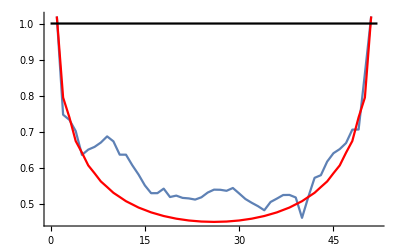

```mathematica
uu=Table[pl=pickLoci[k,0,1,5];Mean[Count[#,1]&/@Transpose[dipInd[0,1,5]⟦All,pl⟧]]//N,{k,1,51}];
rn=Range[1,51];Show[ListLinePlot[uu/(rn(1-rn/52))],ListLinePlot[ftt,PlotStyle->Red],Plot[1,{x,0,52},PlotStyle->Black],PlotRange->All]
```

#### Missing mice do not account for “impossible” SNP

First, consider the effects of missing mice. A rough estimate can be made by focussing on the loci polymorphic in the founders, and then sub-sampling a smaller #, and asking how many SNP are then missed.

For example, in LS1, there are 26774 SNP out of 454176 that are “impossible”:

```mathematica
Length/@{polLoci[{0,17},1,5],polLoci[0,1,5],polLoci[17,1,5],Complement[polLoci[17,1,5],polLoci[0,1,5]],Complement[polLoci[0,1,5],polLoci[17,1,5]]}
```

{454176,427402,383380,26774,70796}

These are the # of SNP polymorphic in the sampled founders; in the sub-sample; at the end; “impossible”; and lost.  There are far fewer missing than in the actual data:

```mathematica
pl=polLoci[0,1,5];fr=Total[RandomSample[dipInd[0,1,5]⟦All,pl⟧,24]]/48.;
ppl0=Pick[pl,(0<#<1)&/@fr];(* the subset polymprphic in the subsample *)
ipl=Intersection[pl,polLoci[17,1,5]];
Length/@{pl,ppl0,ipl,Complement[ipl,ppl0],Complement[ppl0,ipl]}
```

{427402,424478,356606,1612,69484}

A replicate:

```mathematica
pl=polLoci[0,1,5];fr=Total[RandomSample[dipInd[0,1,5]⟦All,pl⟧,24]]/48.;
ppl0=Pick[pl,(0<#<1)&/@fr];(* the subset polymprphic in the subsample *)
ipl=Intersection[pl,polLoci[17,1,5]];
Length/@{pl,ppl0,ipl,Complement[ipl,ppl0],Complement[ppl0,ipl]}
```

{427402,424984,356606,1391,69769}

For LS2, three mice were missing from the initial 28, so we must subsample 22 from 25:

```mathematica
Length/@{polLoci[{0,17},2,5],polLoci[0,2,5],polLoci[17,2,5],Complement[polLoci[17,2,5],polLoci[0,2,5]],Complement[polLoci[0,2,5],polLoci[17,2,5]]}
```

{462755,435301,398404,27454,64351}

```mathematica
pl=polLoci[0,2,5];fr=Total[RandomSample[dipInd[0,2,5]⟦All,pl⟧,22]]/44.;
ppl0=Pick[pl,(0<#<1)&/@fr];(* the subset polymprphic in the subsample *)
ipl=Intersection[pl,polLoci[17,2,5]];
Length/@{pl,ppl0,ipl,Complement[ipl,ppl0],Complement[ppl0,ipl]}
```

{435301,427953,370950,3319,60322}

#### Mis-assignment of heterozygotes

Suppose that we take the actual distribution, and generate a ‘true’ population that is in HW.  Then, mis-assign heterozygotes, and ask how many SNP now appear to be “impossible”.

Now, loci at p will be re-assigned to {q^2+pqF,2pq(1-F),p^2+pqF}, and we will sample the observed frequency from that.  For each SNP, we do this, and find its new frequency.

```mathematica
Dynamic[k]
```

This gives the # SNP polymorphic in the founders; the # polymorphic after reassigning heterozygotes with F=0.451; and the # that are “impossible”.  The latter hardly fluctuates, and is around 14,400.

```mathematica
pp=freqSNPInd[0,1,5]⟦pl⟧;
ipl=Intersection[pl,polLoci[17,1,5]];
```

```mathematica
ff=0.451;
tt=Table[np=({0,1,2}.BinCounts[RandomChoice[{(1-#)^2+#(1-#)ff,2#(1-#)(1-ff),#^2+#(1-#)ff}->{0,1,2},26],{0,3}])&/@pp;
pl0=Pick[pl,(0<#<52)&/@np];
Length/@{pl,pl0,Complement[ipl,pl0]},{k,5}];
tt//TableForm
```

427402 | 400523 | 14392
427402 | 400463 | 14384
427402 | 400206 | 14497
427402 | 400071 | 14600
427402 | 400409 | 14403

The same, but only with F=0:

```mathematica
ff=0;
tt0=Table[np=({0,1,2}.BinCounts[RandomChoice[{(1-#)^2+#(1-#)ff,2#(1-#)(1-ff),#^2+#(1-#)ff}->{0,1,2},26],{0,3}])&/@pp;
pl0=Pick[pl,(0<#<52)&/@np];
Length/@{pl,pl0,Complement[ipl,pl0]},{k,5}];
tt0//TableForm
```

427402 | 408023 | 9957
427402 | 407841 | 10036
427402 | 407961 | 10065
427402 | 407882 | 10206
427402 | 407876 | 10022

The above procedure is too crude.  Better, work with the configurations {i_1,i_2}, and estimate the “true” density of those configurations.  Then, ask the probability that a SNP with a certain configuration has some “true” configuration, and reassign accordingly.

#### Summary

For LS1, removing two mice from the sample only generates ~ 1500 “impossible” SNP, compared with 27000 observed.  Sampling from the observed frequency distribution with F=0.45 generates ~14,500 impossible SNP, but sampling with F=0 generates ~10000.  This is procedure is too crude, but it is hard to do better without simulating the full process.

### Running simulations

#### Running 3×20 pairs of simulations (quite fast)

There is an annoying and mysterious bug, such that occasionally, the simulation fails at selectKids[].  For the moment, I just ignore this: some simulations just fail.  selectKids[] needs to be fixed: I guess the problem is that the random choice of kids sometimes does not fit the constraints later.

This runs simulations for LS1 and LS2. There are 5 replicates for each, for genetic variance θ=0,1,2 times the estimated V_s=0.584, making 2*3*3=18 simulations.  Note that for each of the 3*3 pairs of simulations, a single population is chosen, and stored as pop[θ,rep]. (Bad practice here, since pop is also a named local variable. OK but best fixed).

Below, I use the fortuitous coincidence that initial numbers are the same in LS1, LS2. Therefore, I can use the same population. Otherwise, I would need to subsample from some larger population.  In general, one would like to explore sub-sampling.  At one extreme, one would sample from an infinitely large population (in which case there would be no replication of the selection response under the infinitesimal model), through to starting with the exact same population (as below), which maximises replicability of the selection response. Note that the issue here is the relation between the initial selected loci; there is a separate choice of the initial SNP.

```mathematica
Dynamic[{r,jθ,rep}]
```

```mathematica
clearGlobalVariables[];resetVariables[];
θl={0,1,2};nreps=20;chrom=5;nloci=10^4;n0=28;
Vs=0.584;ϕ=mouseMap[chrom]/Total[mouseMap[]];(* ϕ is the fraction of genome on the focal chromosome *)
Timing[Do[
θθ=θl⟦jθ⟧;
j0=ConstantArray[n0,nloci];
pop[θθ,rep]=makePopDiploidExact[j0,n0];
α=makeAllelicEffects[nloci];
p0=j0/(2n0)//N;fα=α √((2Vs ϕ θθ)/(2(α^2).(p0(1-p0))));
Do[
ss=sim[r,θθ,rep];
allelicEffects[ss[chrom]]=fα;
makeMouseReps[ss,r,chrom,pop[θθ,rep],fα,Vs,FractionOfVariance->θθ],
{r,2}],{jθ,Length[θl]},{rep,nreps}];]
```

{902.781,Null}

#### Generating shuffled founder haplotypes: makeThrow

makeThrow generates a random reference founder population - a large array of fake haplotypes - using makeFounders[r,c,t,rr,LD].  Haplotypes from LS1 are used to construct these founders, though these are very similar to LS2. Then, the initial and final numbers for LS1, LS2 are stored in nThrow[]. Note that a pair of simulations is supplied, for the two selected lines: {sim[1,1,1][chrom],sim[2,1,1][chrom]}. This procedure stores only the final numbers, not the initial array of fake haplotypes, to save memory.  All this is done by calling makeThrow[], which sets up nThrow[]

This makes one throw of the SNP onto the two lines, with LD:

```mathematica
Clear[nThrow];
Timing[makeThrow[sim[#,1,1][chrom]&/@{1,2},chrom,0,{1,2},LD,1];]
```

{25.5366,Null}

A more efficient way to do this is to make a single set of haplotypes, and then use this multiple times.  This sets up 5 throws each, onto 20 replicate simulations, but using the same founder haplotypes (reshuffled for each seed).  This is the limiting step, for both time and (?) memory:

```mathematica
Timing[hapsLD=makeFounders[1,chrom,0,{1,2},LD];]
```

{5.71453,Null}

```mathematica
Dynamic[{s,rep}]
```

```mathematica
nThrowReps=5;
Timing[Table[makeThrow[hapsLD,sim[#,1,rep][chrom]&/@{1,2},chrom,0,{1,2},LD,s],{s,nThrowReps},{rep,nreps}];]
```

{2296.1,Null}

#### The simulated distribution of Δz^2

This shows the distribution of Δz^2 in 100kb windows, for 5 throws onto each of 20 simulations; the latter are indicated by colour.

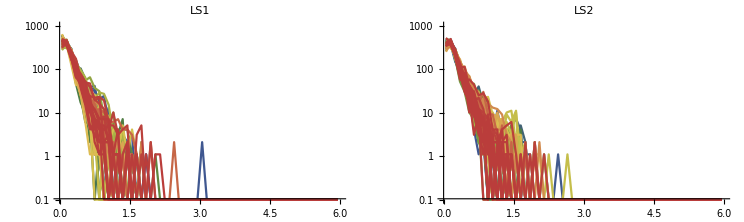

```mathematica
cd=ColorData["DarkRainbow"];dzm=6;GraphicsRow[Table[Show[Table[ListLogPlot[Transpose[{Range[0.05,dzm-0.05,0.1],0.1+BinCounts[dzWinPol[r,hapsLD,sim[r,1,rep][chrom],chrom,2,10^5,0,{1,2},30,LD,s]⟦All,2⟧,{0,dzm,0.1}]}],Joined->True,PlotStyle->cd[(rep-1)/(nreps-1)],PlotLabel->"LS"<>ToString[r],PlotRange->{{0,dzm},{0.1,1000}}],{rep,nreps},{s,nThrowReps}]],{r,1,2}]]
```

This shows the same, but summed over throws, to give the net distribution for each simulation. The thick line shows the overall mean:

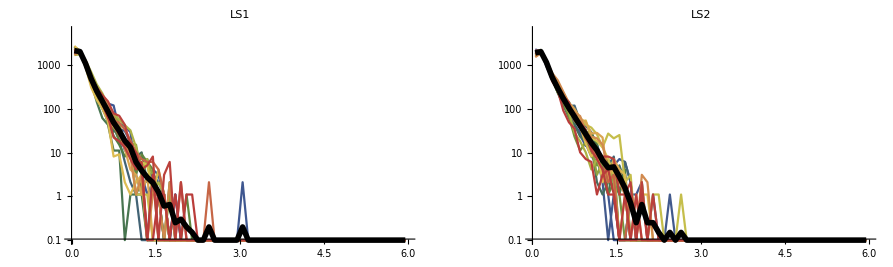

```mathematica
cd=ColorData["DarkRainbow"];dzm=6;GraphicsRow[Table[Show[Table[ListLogPlot[Transpose[{Range[0.05,dzm-0.05,0.1],0.1+Sum[BinCounts[dzWinPol[r,hapsLD,sim[r,1,rep][chrom],chrom,2,10^5,0,{1,2},30,LD,s]⟦All,2⟧,{0,dzm,0.1}],{s,nThrowReps}]}],Joined->True,PlotStyle->cd[(rep-1)/(nreps-1)],PlotLabel->"LS"<>ToString[r],PlotRange->{{0,dzm},{0.1,6000}}],{rep,nreps}],
ListLogPlot[Transpose[{Range[0.05,dzm-0.05,0.1],0.1+1/nreps Sum[BinCounts[dzWinPol[r,hapsLD,sim[r,1,rep][chrom],chrom,2,10^5,0,{1,2},30,LD,s]⟦All,2⟧,{0,dzm,0.1}],{rep,nreps},{s,nThrowReps}]}],Joined->True,PlotStyle->{Thickness[0.01],Black},PlotLabel->"LS"<>ToString[r],PlotRange->{{0,dzm},{0.1,6000}}]],{r,1,2}]]
```

This compares the net distribution (black) with the observations (red):

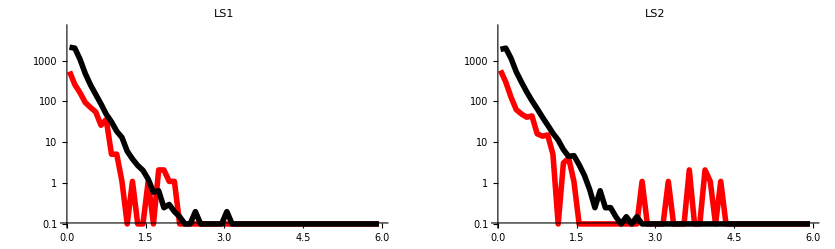

```mathematica
cd=ColorData["DarkRainbow"];dzm=6;GraphicsRow[Table[Show[ListLogPlot[Transpose[{Range[0.05,dzm-0.05,0.1],0.1+BinCounts[dzWinPol[r,chrom,2,10^5,0,{1,2},30]⟦All,2⟧,{0,dzm,0.1}]}],Joined->True,PlotStyle->{Thickness[0.01],Red},PlotLabel->"LS"<>ToString[r],PlotRange->{{0,dzm},{0.1,6000}}],
ListLogPlot[Transpose[{Range[0.05,dzm-0.05,0.1],0.1+1/nreps Sum[BinCounts[dzWinPol[r,hapsLD,sim[r,1,rep][chrom],chrom,2,10^5,0,{1,2},30,LD,s]⟦All,2⟧,{0,dzm,0.1}],{rep,nreps},{s,nThrowReps}]}],Joined->True,PlotStyle->{Thickness[0.01],Black},PlotLabel->"LS"<>ToString[r],PlotRange->{{0,dzm},{0.1,6000}}]],{r,1,2}]]
```

#### Some examples: genome scan and scatter plot

This compares a simulated genome scan (top) with the data (bottom):

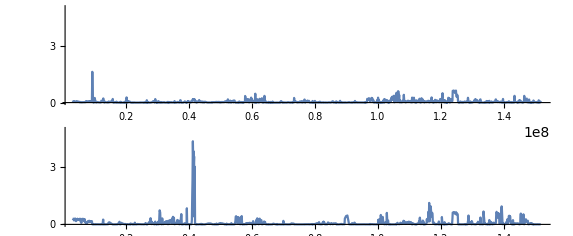

```mathematica
GraphicsColumn[{ListLinePlot[dzWinPol[1,sim[1,1,1][chrom],chrom,2,10^5,0,{1,2},30,LD,1]/.{x_,y_}:>{x,y^2},AspectRatio->0.2,PlotRange->{All,{0,5}}],
ListLinePlot[dzWinPol[1,chrom,2,10^5,0,{1,2},30]/.{x_,y_}:>{x,y^2},AspectRatio->0.2,PlotRange->{All,{0,5}}]}]
```

This compares the scatter plots for simulation (top) vs data (bottom):

```mathematica
dzWinPol[2,sim[2,1,1][chrom],chrom,10^5,0,{1,2},30,LD,1]⟦All,2⟧
```

Thread::tdlen: Objects of unequal length in {0.674131,0.,0.355421,0.355421,0.674131,0.674131,0.674131,0.355421,0.895665,0.895665,«32»,0.674131,0.622368,0.622368,0.355421,0.355421,0.355421,0.674131,0.250656,«431631»}+{«1»} cannot be combined.

Part::partw: Part {5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,«162»} of {0.674131,0.,0.355421,0.355421,0.674131,0.674131,0.674131,0.355421,0.895665,0.895665,«32»,0.674131,0.622368,0.622368,0.355421,0.355421,0.355421,0.674131,0.250656,«431631»}+{«1»} does not exist.

Part::partw: Part {217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,«229»} of {0.674131,0.,0.355421,0.355421,0.674131,0.674131,0.674131,0.355421,0.895665,0.895665,«32»,0.674131,0.622368,0.622368,0.355421,0.355421,0.355421,0.674131,0.250656,«431631»}+{«1»} does not exist.

Part::partw: Part {496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,«374»} of {0.674131,0.,0.355421,0.355421,0.674131,0.674131,0.674131,0.355421,0.895665,0.895665,«32»,0.674131,0.622368,0.622368,0.355421,0.355421,0.355421,0.674131,0.250656,«431631»}+{«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

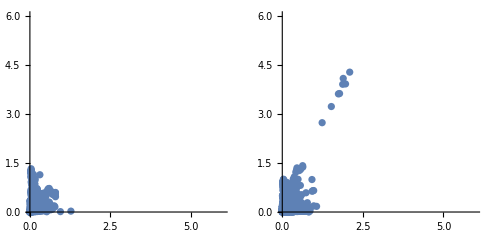

```mathematica
GraphicsRow[{ListPlot[Transpose[(dzWinPol[#,sim[#,1,1][chrom],chrom,2,10^5,0,{1,2},30,LD,1]⟦All,2⟧)&/@{1,2}],AspectRatio->1,PlotStyle->PointSize[0.013],PlotRange->{{0,6},{0,6}}],
ListPlot[Transpose[(dzWinPol[#,chrom,2,10^5,0,{1,2},30]⟦All,2⟧)&/@{1,2}],AspectRatio->1,PlotStyle->PointSize[0.013],PlotRange->{{0,6},{0,6}}]}]
```

#### Constructing the transition probabilities (in progress)

nThrow[t,r,haps,sim[1,1,1][c],c,0,{1,2},LD,1] gives the actual initial sampled frequencies in LS1; I always use the SNP from LS1, to maximise replicability.  nThrow[t,r,haps,sim[1,1,1][c],c,0,{1,2},LD,1] stores the true initial frequencies in the fake haplotypes, constructed from line 1.  nThrow[17,r,haps,sim[r,θ,rep][c],c,0,{1,2},LD,1]  stores the final frequencies for simulation sim[r,θ,rep][chrom], starting with haplotypes constructed from line r0

```mathematica
nThrow[0,1,hapsLD,sim[1,1,1][chrom],chrom,0,{1,2},LD,1]//Length
```

464338

```mathematica
n0Obs
```

All we need store is the transition probabilities (which can be defined in two alternative ways). This uses the sampled allele frequencies, and is closest to the actual observations:

```mathematica
tpS=BinCounts[Transpose[{pp0S,pp17[1,1,1,1,LE,1]}],{0,53},{0,65}];tpS//Dimensions
```

{53,65}

This uses the true initial allele frequencies (including the missing mice):

```mathematica
tp[r_,θ_,rep_,m_,seed_]:=tp[r,θ,rep,m,seed]=Module[{n0=Length[dipInd[0,r,chrom]],
n1=Length[dipInd[17,r,chrom]]},
BinCounts[Transpose[{pp0[r,m,seed],pp17[r,1,θ,rep,m,seed]}],{0,2n0+1},{0,2n1+1}]];
```

transitionProb

```mathematica
transitionProb::usage="transitionProb[";
```

Global`trans

#### Comparing variability between throws with variability between simulations, for Pr[j_0→j_17]

This compares two methods for throwing down SNP: independently (LE; blue), vs. with LD (red). For each method, there were  5 replicate throws of SNP onto a single simulation. Plots show the distribution of the final #, given an initial # of 5, 20 (left, right); θ=1 (i.e., infinitesimal selection with the estimated V_s.  Note the substantially higher variation when the founder SNP are in LD. SImulations are for LS1.

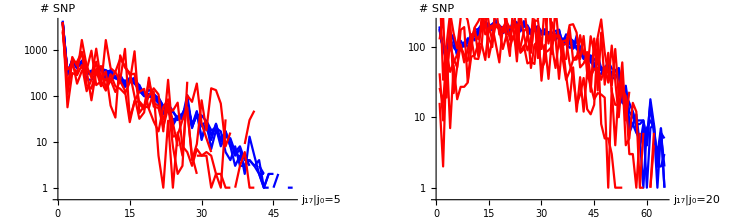

```mathematica
gr[j0_]:=Show[MapThread[Table[ListLogPlot[tp[1,1,1,#1,s]⟦j0+1⟧,Joined->True,PlotStyle->#2],{s,5}]&,{{LE,LD},{Blue,Red}}],AxesLabel->{"j_17|j_0="<>ToString[j0],"# SNP"}];
GraphicsRow[gr/@{5,20}]
```

This makes a single throw onto three replicate simulations.  A rough impression is that there is somewhat less variation between simulations than between replicate throws of SNP onto the same simulation (above).

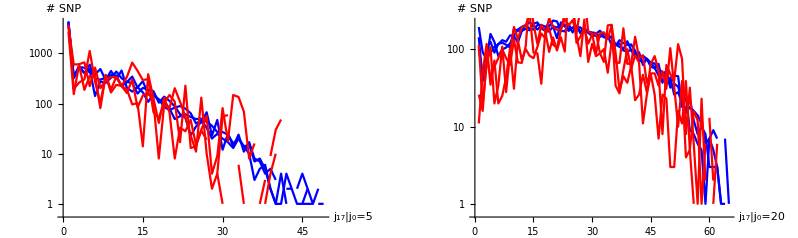

```mathematica
gr2[j0_]:=Show[MapThread[Table[ListLogPlot[tp[1,1,k,#1,1]⟦j0+1⟧,Joined->True,PlotStyle->#2],{k,3}]&,{{LE,LD},{Blue,Red}}],AxesLabel->{"j_17|j_0="<>ToString[j0],"# SNP"}];
GraphicsRow[gr2/@{5,20}]
```

#### Replication between LS1, LS2

```mathematica
Clear[dz];
dz[r_,r0_,θ_,rep_,m_,seed_]:=dz[r,r0,θ,rep,m,seed]=Module[{n0=Length[pedigree[r]⟦17⟧],
n1=Length[pedigree[r]⟦17⟧]},
arcsin[pp17[r,r0,θ,rep,m,seed]/(2.n1)]-arcsin[pp0[r,m,seed]/(2.n0)]];
```

This is a very large graphic - reduced to BitMap to save memory

Note that windows here count only polymorphic loci - different from the above.  The values generated by LE (left) show less dispersion, but also a stronger correlation. It is not clear whether this correlation reflects replication of the selection response under the infinitesimal model: it might simply be that windows carry different combinations of SNP, that allow different distributions of Δz^2.  That could be tested by looking at neutral simulations.

```mathematica
pL=polLoci[0,{1,2},chrom];
wn30=Select[GatherBy[Range[Length[pL]],Round[posSNPInd[chrom]⟦pL⟦#⟧⟧/10^4]&],Length[#]>30&];
  cd=ColorData["DarkRainbow"];
xx2={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,1,1,LD,1]⟦#⟧)^2],Mean[(dz[2,1,1,1,LD,1]⟦#⟧)^2]}]}&/@wn30;
xx2LE={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,1,1,LE,1]⟦#⟧)^2],Mean[(dz[2,1,1,1,LE,1]⟦#⟧)^2]}]}&/@wn30;
GraphicsRow[Show[Graphics[Join[{PointSize[0.007]},#]],AspectRatio->1,Axes->True,AxesLabel->{"Δz_1^2","Δz_2^2"},PlotRange->{{0,2.5},{0,2.5}},AxesOrigin->{0,0}]&/@{xx2LE,xx2}]
```

-Graphics-

This shows neutral simulations. Note the same asymmetry as above between LS1 and LS2 distributions; and also, an evident correlation in the LE plots (left).  One needs more replicates to make sense of this.

```mathematica
pL=polLoci[0,{1,2},chrom];
wn30=Select[GatherBy[Range[Length[pL]],Round[posSNPInd[chrom]⟦pL⟦#⟧⟧/10^4]&],Length[#]>30&];
  cd=ColorData["DarkRainbow"];
xx2N={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,0,1,LD,1]⟦#⟧)^2],Mean[(dz[2,1,0,1,LD,1]⟦#⟧)^2]}]}&/@wn30;
xx2NLE={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,0,1,LE,1]⟦#⟧)^2],Mean[(dz[2,1,0,1,LE,1]⟦#⟧)^2]}]}&/@wn30;
GraphicsRow[Show[Graphics[Join[{PointSize[0.007]},#]],AspectRatio->1,Axes->True,AxesLabel->{"Δz_1^2","Δz_2^2"},PlotRange->{{0,2.5},{0,2.5}},AxesOrigin->{0,0}]&/@{xx2NLE,xx2N}]
```

-Graphics-

For comparison, here are the data: note the different scales.  The joint distribution of Δz^2 (right) is in bulk vaguely similar to that generated by simulation with LD (above), though possibly with less clumping; the candidate at 41-42Mb is a very clear outlier.

-Graphics-

#### Genome scans: 10kb windows

This sets up 10kb windows containing at least 30 SNP, using the loci polymorphic in the founders.  I do not use winInd, because that uses the full list of SNP, and is very inefficient.

```mathematica
pL=polLoci[0,{1,2},chrom];
wn30=Select[GatherBy[Range[Length[pL]],Round[posSNPInd[chrom]⟦pL⟦#⟧⟧/10^4]&],Length[#]>30&];
```

This shows the actual data in LS1, LS2:

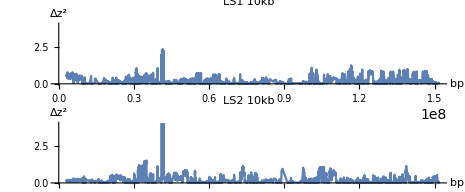

```mathematica
Clear[dzObs,dzzObs];
 dzObs[r_]:=dzObs[r]=N[arcsin[freqSNPInd[17,r,5]⟦pL⟧]-arcsin[freqSNPInd[0,r,5]⟦pL⟧]];
dzzObs[r_]:=dzzObs[r]=N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[(dzObs[r]⟦#⟧)^2]}]&/@wn30;
GraphicsColumn[ListLinePlot[dzzObs[#],AspectRatio->0.2,PlotRange->{Automatic,{0,4}},PlotLabel->"LS"<>ToString[#1]<>" 10kb",AxesLabel->{"bp","Δz^2"}]&/@{1,2}]
```

This shows one pair of simulations, with SNP thrown down at random:

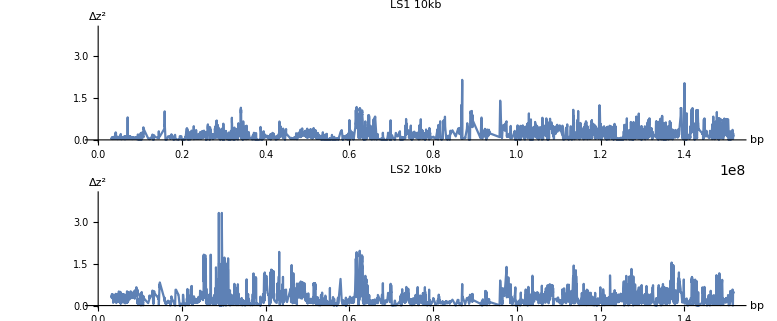

```mathematica
dz[r_,r0_,θ_,rep_,m_,seed_]:=dz[r,r0,θ,rep,m,seed]=
Module[{n0=Length[pedigree[r]⟦17⟧],n1=Length[pedigree[r]⟦17⟧]},
arcsin[pp17[r,r0,θ,rep,m,seed]/(2.n1)]-arcsin[pp0[r,m,seed]/(2.n0)]]; dzz[r_,θ_,rep_,m_,seed_]:=dzz[r,θ,rep,m,seed]=N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[(dz[r,1,θ,rep,m,seed]⟦#⟧)^2]}]&/@wn30;
GraphicsColumn[ListLinePlot[dzz[#,1,1,LD,1],AspectRatio->0.2,PlotRange->{Automatic,{0,4}},PlotLabel->"LS"<>ToString[#1]<>" 10kb",AxesLabel->{"bp","Δz^2"}]&/@{1,2}]
```

#### Distribution of Δz^2: 10kb windows

The top row compares the observed distribution of mean Δz^2 in 10kb windows, for LS1, LS2 (red, orange) with three replicate simulation pairs (LS1, LS2 black, blue). The middle row shows three replicate throws of SNP onto one pair of simulations, assuming LD. The last row does the same, assuming LE.  The bulk of the distribution (up to Δz^2=1.5, say) seems similar, suggesting that the model is correct. The degree of variation between simulations  (top) and between throws with LD (middle) seem similar, and include the observed Δz^2 for LS1, but not LS2.  Throws with LE show far less variation. However, the observations are more significant than this plot suggests, because i) the outlier windows are contiguous and ii) they are the same for LS1 and for LS2.

```mathematica
grObs[r_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzzObs[r]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->{Thickness[0.006],c}];gr[r_,rep_,m_,seed_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzz[r,1,rep,m,seed]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->c];GraphicsColumn[{Show[
gr[1,#,LD,1,Black]&/@{1,2,3},gr[2,#,LD,1,Blue]&/@{1,2,3},
MapThread[grObs,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 simulations"],
Show[
gr[1,1,LD,#,Black]&/@{1,2,3},gr[2,1,LD,#,Blue]&/@{1,2,3},
MapThread[grObs,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 throws of SNP in LD"],
Show[
gr[1,1,LE,#,Black]&/@{1,2,3},gr[2,1,LE,#,Blue]&/@{1,2,3},
MapThread[grObs,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 throws of SNP in LE"]}]
```

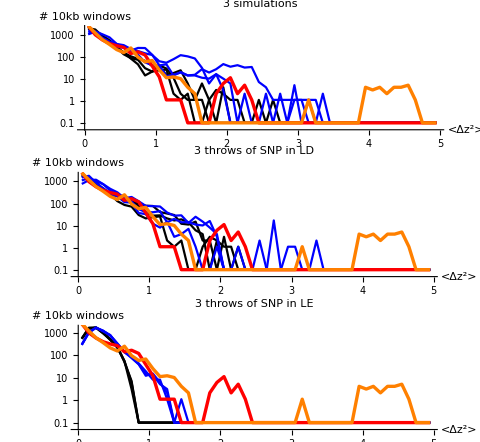

#### Genome scans and distributions of Δz^2: 100kb windows

```mathematica
wn300=Select[GatherBy[Range[Length[pL]],Round[posSNPInd[chrom]⟦pL⟦#⟧⟧/10^5]&],Length[#]>300&];
dzzObs300[r_]:=dzzObs300[r]=N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[(dzObs[r]⟦#⟧)^2]}]&/@wn300;
dzz300[r_,θ_,rep_,m_,seed_]:=dzz300[r,θ,rep,m,seed]=N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[(dz[r,1,θ,rep,m,seed]⟦#⟧)^2]}]&/@wn300;
```

This shows genome scans as above, but in 100kb windows (including windows with >300 SNP). The peak at 41Mb is apparent in both LS1 and LS2 in the real data (top two rows). In one simulation pair (lower two rows), with SNP thrown down in LD, peaks are lower, but there is still a replicated peak at 60Mb (for example)

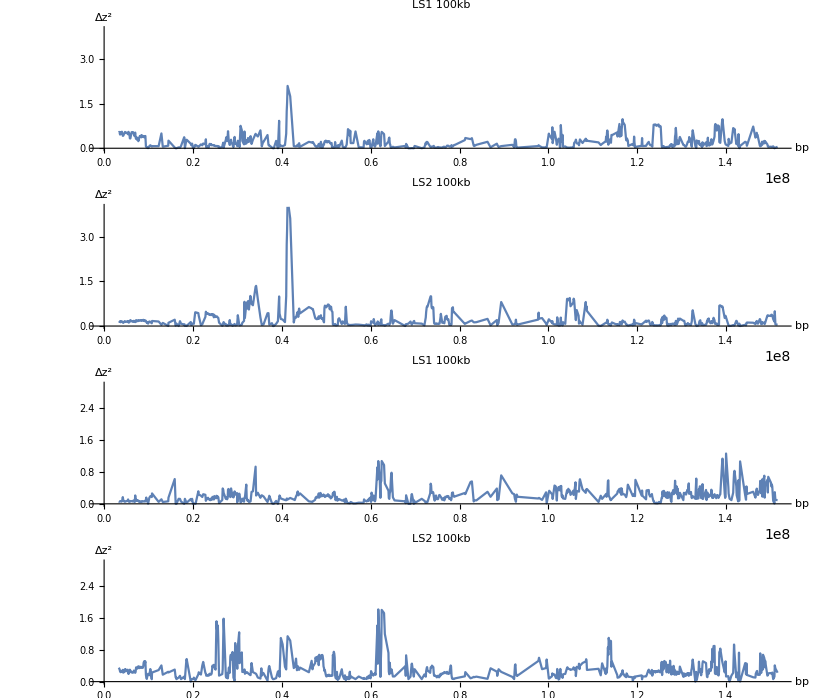

```mathematica
GraphicsColumn[Join[ListLinePlot[dzzObs300[#],AspectRatio->0.2,PlotRange->{Automatic,{0,4}},PlotLabel->"LS"<>ToString[#1]<>" 100kb",AxesLabel->{"bp","Δz^2"}]&/@{1,2},ListLinePlot[dzz300[#,1,1,LD,1],AspectRatio->0.2,PlotRange->{Automatic,{0,3}},PlotLabel->"LS"<>ToString[#1]<>" 100kb",AxesLabel->{"bp","Δz^2"}]&/@{1,2}]]
```

This shows the distribution of Δz^2 in 100kb, in the same way as above.  The outlier in LS1 (red) is within the range of variation of simulated data, but the LS2 outlier is outside that range (though one would need more simulations to be sure).

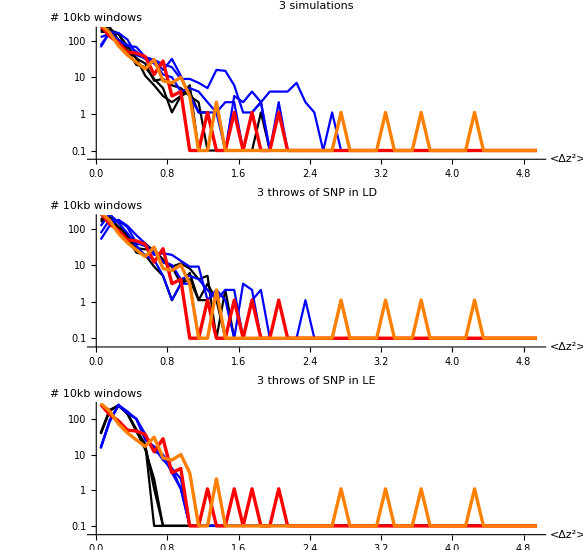

```mathematica
grObs300[r_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzzObs300[r]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->{Thickness[0.006],c}];gr300[r_,rep_,m_,seed_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzz300[r,1,rep,m,seed]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->c];GraphicsColumn[{Show[
gr300[1,#,LD,1,Black]&/@{1,2,3},gr300[2,#,LD,1,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 simulations"],
Show[
gr300[1,1,LD,#,Black]&/@{1,2,3},gr300[2,1,LD,#,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 throws of SNP in LD"],
Show[
gr300[1,1,LE,#,Black]&/@{1,2,3},gr300[2,1,LE,#,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
AspectRatio->0.3,AxesLabel->{"<Δz^2>","# 10kb windows"},PlotLabel->"3 throws of SNP in LE"]}]
```

#### Testing the significance of replicated sweeps

Looking at each population separately, the strong peak in LS1 does not seem significant - whereas that in LS2 is.  What is striking, though, is that the two peaks are in the same place.  How to test this?  One way would be to ask about the overlap in location between windows above a certain threshold value.

```mathematica
ssObs[r_,t_]:=Pick[Range[Length[dzzObs[r]]],#⟦2⟧≥t&/@dzzObs[r]];
```

```mathematica
ssSim[r_,rep_,m_,seed_,t_]:=Pick[Range[Length[dzz[r,1,rep,m,seed]]],#⟦2⟧≥t&/@dzz[r,1,rep,m,seed]];
```

```mathematica
coincidenceObs[t_]:=(Length[wn30]Length[Intersection[ssObs[1,t],ssObs[2,t]]])/(Length[ssObs[1,t]]Length[ssObs[2,t]])//N;
```

```mathematica
coincidenceSim[rep_,m_,seed_,t_]:=Module[{nn=Length[wn30],n1=Length[ssSim[1,rep,m,seed,t]],n2=Length[ssSim[2,rep,m,seed,t]],n12=Length[Intersection[ssSim[1,rep,m,seed,t],ssSim[2,rep,m,seed,t]]]},
If[n12==0,0,(nn n12)/(n1 n2)//N]];
```

This counts the # of 10kb windows with >30 SNP; the # of those with Δz^2>2 in LS1 and in LS2; and the # of windows with value>2 in both LS1 and LS2. The last # is the ratio between the observed # of coincidences, and the expected #:

```mathematica
{Length/@{wn30,ssObs[1,t],ssObs[2,t],Intersection[ssObs[1,t],ssObs[2,t]]},coincidenceObs[2]}
```

{{5546,0,0,0},198.071}

This calculates the obs/expected # of coincidences for 3 pairs of simulations, and 3 throws of  the SNP for each pair.  There are no coincidences at all.

```mathematica
cc=Outer[coincidenceSim[#1,LD,#2,2]&,{1,2,3},{1,2,3},1];
{cc,coincidenceObs[2]}
```

{{{0,0,0},{0,0,0},{0,0,0}},198.071}

This is the same, but with a threshold at Δz^2=1:

```mathematica
cc=Outer[coincidenceSim[#1,LD,#2,1]&,{1,2,3},{1,2,3},1];
{cc,coincidenceObs[1]}
```

{{{6.91349,1.86514,2.31373},{0,0,0},{3.71005,5.17061,6.22059}},41.6237}

This needs many more replicates to test significance - if this is a good approach.

#### Haplotype diversity and plots of the genomes

This shows the haplotype homozygosity along the genome (inset at right) for LS1, LS2 in one simulation (blue, red). In LS2  there is a peak around 0.13-0.16, and in LS1, around 0.5.

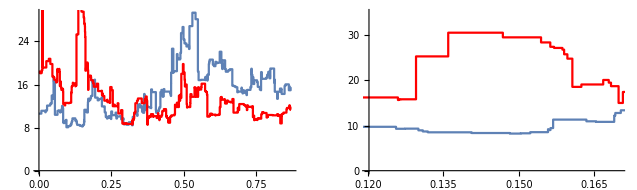

```mathematica
cA=configIntervalsAnc[sim[1,1,1][5],17];
xx=locJ[sim[1,1,1][5]]/@allJunctions[sim[1,1,1][5],17];
hd=Total/@(cA^2)/64.;
cA2=configIntervalsAnc[sim[2,1,1][5],17];
xx2=locJ[sim[2,1,1][5]]/@allJunctions[sim[2,1,1][5],17];
hd2=Total/@(cA2^2)/64.;
GraphicsRow[{Show[ListLinePlot[Flatten[Transpose[Transpose/@{{Drop[xx,-1],hd},{Drop[xx,1],hd}}],1]],ListLinePlot[Flatten[Transpose[Transpose/@{{Drop[xx2,-1],hd2},{Drop[xx2,1],hd2}}],1],PlotStyle->Red]],
Show[ListLinePlot[Flatten[Transpose[Transpose/@{{Drop[xx,-1],hd},{Drop[xx,1],hd}}],1],PlotRange->{{0.12,0.17},{0,35}}],
ListLinePlot[Flatten[Transpose[Transpose/@{{Drop[xx2,-1],hd2},{Drop[xx2,1],hd2}}],1],PlotStyle->Red],PlotRange->{{0.12,0.17},{0,35}}]}]
```

There are no obvious sweeps: the peak in LS2 (above) seems to be due to increases of a number of ancestral genomes:

```mathematica
GraphicsColumn[plotGenomes[sim[#,1,1][5],17,0.004,AspectRatio->0.3]&/@{1,2}]
```

-Graphics-

```mathematica
plotGenomes[sim[1,1,2][5],17,0.004,AspectRatio->0.3]
```

-Graphics-

```mathematica
plotGenomes[sim[2,1,1][5],17,0.014,AspectRatio->1,PlotRange->{{0.12,0.7},{0,1}}]
```

-Graphics-

#### Trait values in three replicate simulations

These are the initial and final  trait mean & variance in LS1, LS2:

```mathematica
zt[t_,r_,θ_,rep_]:=z[allelicEffects[sim[r,θ,rep][5]]]/@Flatten[pop[sim[r,θ,rep][5]]⟦t+1⟧,1];
Flatten[Table[{"rep "<>ToString[k],"LS"<>ToString[#],Mean[zt[0,#,1,k]],Mean[zt[17,#,1,k]],Variance[zt[0,#,1,k]],Variance[zt[17,#,1,k]]}&/@{1,2},{k,3}],1]//Chop//TableForm
```

rep 1 | LS1 | 0 | 0.353005 | 0.0442207 | 0.032406
rep 1 | LS2 | 0 | 0.376466 | 0.0442207 | 0.0253501
rep 2 | LS1 | 0 | 0.0681499 | 0.0372952 | 0.0293191
rep 2 | LS2 | 0 | 0.194827 | 0.0372952 | 0.041863
rep 3 | LS1 | 0 | 0.279174 | 0.0318388 | 0.0352345
rep 3 | LS2 | 0 | 0.280682 | 0.0318388 | 0.0224843

This is the correlation of effect across loci for the three replicates- very weak, because the contribution is largely noise under this near-infinitesimal model:

```mathematica
aa[r_,θ_,rep_]:=allelicEffects[sim[r,θ,rep][5]];
locZ[r_,θ_,rep_]:=(Span@@(locPos[10^4,mouseMap[5]][#]))&/@dxx[r,θ,rep];
pzl[r_,θ_,rep_]:=(Mean[Flatten[pop[sim[r,θ,rep][5]]⟦18⟧,1]]-1/2);
Correlation[pzl[1,1,#],pzl[2,1,#]]&/@{1,2,3}//N
```

{0.017885,0.0150773,-0.0529017}

This is the contribution of each interval in LS1 and LS2 for three simulations. In the first row, there is no sign of any particular contribution in LS2 around 0.145, as would be expected if selection drove that peak in loss of haplotype diversity:

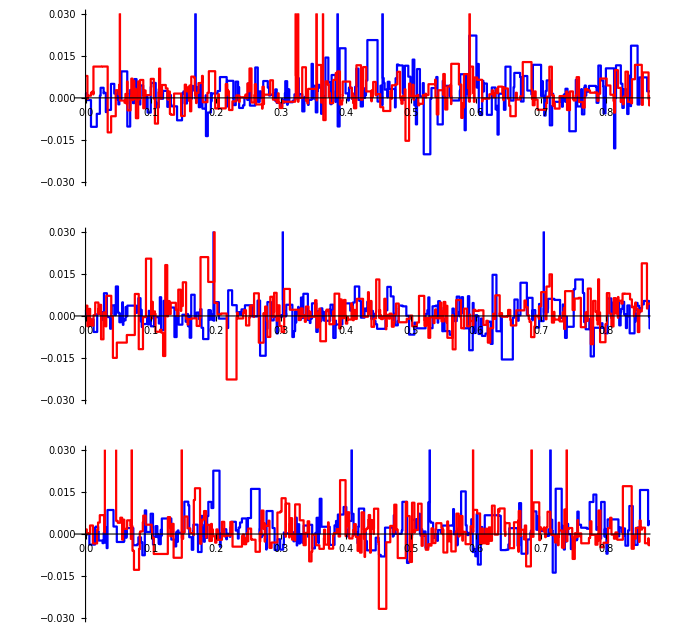

```mathematica
zm[r_,θ_,rep_]:=(pzl[r,θ,rep]⟦#⟧.aa[r,θ,rep]⟦#⟧)&/@locZ[r,θ,rep];
GraphicsColumn[Table[Show[Table[ListLinePlot[Flatten[MapThread[{{#1⟦1⟧,#2},{#1⟦2⟧,#2}}&,{dxx[r,1,k],zm[r,1,k]}],1],PlotStyle->{Blue,Red}⟦r⟧,AspectRatio->0.3,PlotRange->{{0,0.85},{-0.03,0.03}}],{r,1,2}]],{k,3}]]
```

#### Haplotype diversity in three replicate simulations

This shows the haplotype homozygosity along the genome (inset at right) for LS1, LS2  (blue, red) in three replicate simulations.

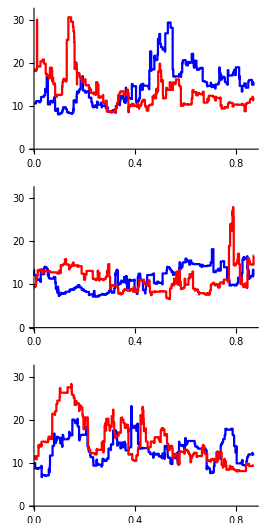

```mathematica
cA[r_,θ_,rep_]:=configIntervalsAnc[sim[r,θ,rep][5],17];
xx[r_,θ_,rep_]:=locJ[sim[r,θ,rep][5]]/@allJunctions[sim[r,θ,rep][5],17];
tdxx[r_,θ_,rep_]:=Flatten[Transpose[Transpose/@{{Drop[xx[r,θ,rep],-1],hd[r,θ,rep]},{Drop[xx[r,θ,rep],1],hd[r,θ,rep]}}],1];
dxx[r_,θ_,rep_]:=Transpose[{Drop[xx[r,θ,rep],-1],Drop[xx[r,θ,rep],1]}];
hd[r_,θ_,rep_]:=Module[{ca=cA[r,θ,rep],n1},
n1=Total[ca⟦1⟧];Total/@(ca^2)/n1//N];
GraphicsColumn[Table[Show[MapThread[ListLinePlot[tdxx[#1,1,k],PlotStyle->#2,PlotRange->{{0,0.87},{0,32}}]&,{{1,2},{Blue,Red}}]],{k,3}]]
```

#### What does the candidate sweep contribute to the selection response?

I need to check carefully the reasoning here, since I worry that I may be losing a factor of 2 in dealing with selection within families, and in calculating trait values for diploids. Also, the total change in mean relative to √V_e seems too large. At face value, the candidate only seems to contribute 1/60 of the response.

I estimate selection on the candidate SNP of ~ {-0.182, -0.323}, with  frequencies 0.822→{0.167, 0.019} in the two lines.  I also estimated a narrow-sense heritability of 0.584, based on covariances between parent & offspring, and on selection response.

Now, I show below that by choosing the top male and the top female out of a litter of 5 sons and 5 daughters, there is an effective selection coefficient of s=1.31α , the allelic effect α being scaled by V_P=1.584.  Therefore, taking the mean selection s= -0.253, we have α/(√V_e)=0.253/1.31 √1.584=0.243.  This single substitution, therefore, is expected to change the mean by 0.486√V_e. Actually, the allele frequencies change by on average 0.729, so the contribution to the change in mean should be 0.354√V_e.  The observed change in the composite trait log[T B^-0.57] averages 0.123 in absolute value, and I estimate V_e=0.0000334, or √V_e=0.0058.  Therefore, the total response over 17 generations is Δz̄/√V_e= 21.3.  The contribution of the locus on chromosome 5 is thus estimated as 0.017~1/60 of the total - or 1/3 of a chromosome’s worth.

Actually, V_e is an underestimate - it is taken as the difference of two imprecise measures. Better to take the direct estimate of within-family variance, V_s+V_e=0.000403, so that α=0.253/1.31 √0.00403=0.0122, leading to a predicted contribution 2 0.729 0.0122=0.0178.  This can be compared with OverBar[Δz]=0.123: the candidate sweep contributed 0.145 of the total change in mean (very roughly)

```mathematica
0.123/√0.00403
```

1.93755

```mathematica
2 0.729 0.0122{1,1/0.123}
```

{0.0177876,0.144615}

```mathematica
0.253/1.31 √0.00403
```

0.0122603

```mathematica
(Mean[ztb[0.57,17,#]]-Mean[ztb[0.57,1,#]])&/@{1,2}
```

{0.124338,0.122362}

```mathematica
DeleteCases[{#,Mean[ztb[0.57,#,0]]}&/@Range[17],{_,Mean[{}]}]
```

{{4,2.20261},{7,2.19693},{9,2.19459},{10,2.18332},{12,2.18206},{13,2.18974},{14,2.19181},{15,2.18905},{16,2.18394},{17,2.19286}}

```mathematica
Variance[ztb[0.57,#,2]]&/@Range[20]
```

{0.000524248,0.00037244,0.000568929,0.000742943,0.000449707,0.000472427,0.000445179,0.000436489,0.000314437,0.000620702,0.000654215,0.00132362,0.000459496,0.00579757,0.000440555,0.00041789,0.00042404,0.000393084,0.000396709,0.000274257}

Variance::shlen: The argument {} should have at least two elements.

General::stop: Further output of Variance::shlen will be suppressed during this calculation.

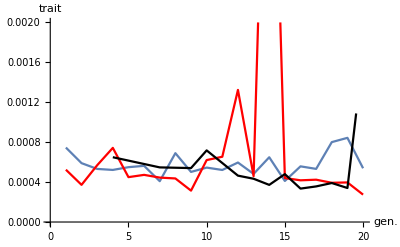

```mathematica
Show[ListLinePlot[Variance[ztb[0.57,#,1]]&/@Range[20],PlotRange->{{0,20},{0,0.002}}],
ListLinePlot[Variance[ztb[0.57,#,2]]&/@Range[20],PlotStyle->Red,PlotRange->{{0,20},{0,0.002}}],ListLinePlot[DeleteCases[{#,Variance[ztb[0.57,#,0]]}&/@Range[20],{_,Variance[{}]}],PlotStyle->Black],AxesOrigin->{0,0},BaseStyle->{FontFamily->"Times",FontSize->14},AxesLabel->{"gen.","trait"}]
```

```mathematica
Mean[Variance[ztb[0.57,#,1]]&/@Range[20]]
```

0.000579092

```mathematica
0.123/√0.000579092046605777
```

5.1113

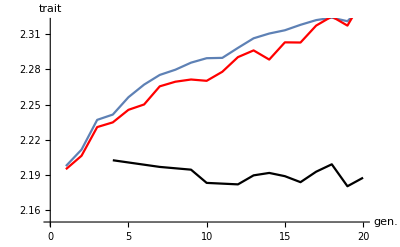

```mathematica
Show[ListLinePlot[Mean[ztb[0.57,#,1]]&/@Range[20]],ListLinePlot[Mean[ztb[0.57,#,2]]&/@Range[20],PlotStyle->Red],ListLinePlot[DeleteCases[{#,Mean[ztb[0.57,#,0]]}&/@Range[20],{_,Mean[{}]}],PlotStyle->Black],PlotRange->{{0,20},{2.15,2.32}},AxesOrigin->{0,2.15},BaseStyle->{FontFamily->"Times",FontSize->14},AxesLabel->{"gen.","trait"}]
```

#### Figure for poster: comparing Δz^2 in LS1, LS2

```mathematica
pL=polLoci[0,{1,2},chrom];
wn30=Select[GatherBy[Range[Length[pL]],Round[posSNPInd[chrom]⟦pL⟦#⟧⟧/10^4]&],Length[#]>30&];
  cd=ColorData["DarkRainbow"];
xx2Sim={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,1,1,LD,1]⟦#⟧)^2],Mean[(dz[2,1,1,1,LD,1]⟦#⟧)^2]}]}&/@wn30;
xx2LE={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(posSNPInd[5]⟦-1,2⟧)],Point[{Mean[(dz[1,1,1,1,LE,1]⟦#⟧)^2],Mean[(dz[2,1,1,1,LE,1]⟦#⟧)^2]}]}&/@wn30;
```

```mathematica
xx2Obs={cd[Mean[posSNPInd[5]⟦pL⟦#⟧,2⟧]/(1.6 10^8)],Point[{Mean[(dzObs[1]⟦#⟧)^2],Mean[(dzObs[2]⟦#⟧)^2]}]}&/@wn30;
```

```mathematica
GraphicsRow[MapThread[Show[Graphics[Join[{PointSize[0.01]},#1]],BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{0,2,4},{0,2,4}},PlotLabel->#3,AspectRatio->1,Axes->True,AxesLabel->{"Δz_1^2","Δz_2^2"},PlotRange->{{0,#2},{0,#2}},AxesOrigin->{0,0}]&,{{xx2Obs,xx2LE,xx2Sim},{5,5,5},{"Observed","SNP in LE","SNP in LD"}}]]
```

-Graphics-

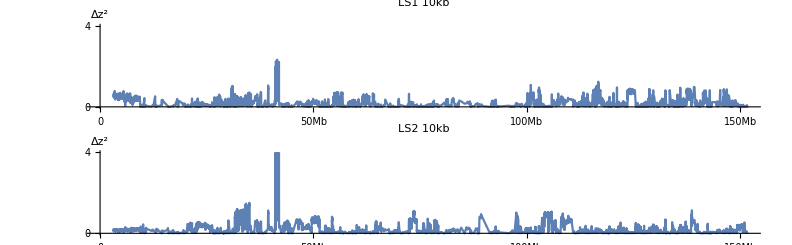

```mathematica
dzObs[r_]:=dzObs[r]=N[arcsin[freqSNPInd[17,r,5]⟦pL⟧]-arcsin[freqSNPInd[0,r,5]⟦pL⟧]];
dzzObs[r_]:=dzzObs[r]=N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[(dzObs[r]⟦#⟧)^2]}]&/@wn30;
GraphicsColumn[ListLinePlot[dzzObs[#],BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{{0,0},{0.5 10^8,"50Mb"},{10^8,"100Mb"},{1.5 10^8,"150Mb"}},{0,2,4}},AspectRatio->0.15,PlotRange->{Automatic,{0,4}},PlotLabel->"LS"<>ToString[#1]<>" 10kb",AxesLabel->{"","Δz^2"}]&/@{1,2}]
```

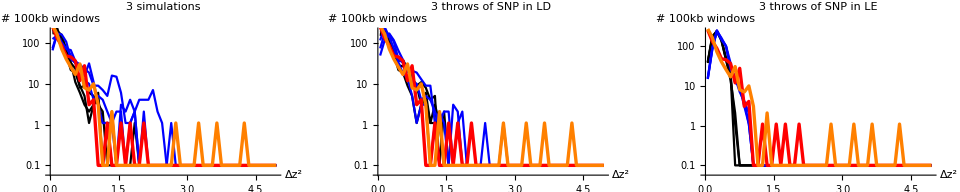

```mathematica
grObs300[r_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzzObs300[r]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->{Thickness[0.006],c}];gr300[r_,rep_,m_,seed_,c_]:=ListLogPlot[Transpose[{Range[0.05,4.95,0.1],0.1+BinCounts[dzz300[r,1,rep,m,seed]⟦All,2⟧,{0,5,0.1}]}],Joined->True,PlotStyle->c];GraphicsRow[{Show[
gr300[1,#,LD,1,Black]&/@{1,2,3},gr300[2,#,LD,1,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->0.6,AxesLabel->{"Δz^2","# 100kb windows"},PlotLabel->"3 simulations"],
Show[
gr300[1,1,LD,#,Black]&/@{1,2,3},gr300[2,1,LD,#,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
BaseStyle->{FontFamily->"Times",FontSize->14}, AspectRatio->0.6,AxesLabel->{"Δz^2","# 100kb windows"},PlotLabel->"3 throws of SNP in LD"],
Show[
gr300[1,1,LE,#,Black]&/@{1,2,3},gr300[2,1,LE,#,Blue]&/@{1,2,3},
MapThread[grObs300,{{1,2},{Red,Orange}}],
BaseStyle->{FontFamily->"Times",FontSize->14}, AspectRatio->0.6,AxesLabel->{"Δz^2","# 100kb windows"},PlotLabel->"3 throws of SNP in LE"]}]
```

### Inferring selection coefficients (not finished)

#### Naive estimation of the selection coefficients for the candidate on chromosome 5: s ~ 25%

This picks out the 10kb windows that have mean Δz^2>2 in both LS1 and LS2, and contain more than 30 SNP:

```mathematica
lw=Length[winPol[chrom,10^4,0,{1,2},30]];
pks=Intersection@@Table[Pick[Range[lw],(#⟦2⟧)^2>2&/@dzWinPol[r,chrom,10^4,0,{1,2},30]],{r,1,2}]
```

{1618,1622,1624,1625,1626,1630,1631,1633,1637,1638,1640,1641,1642,1643}

These are the SNP in those windows:

```mathematica
pkSNP=Flatten[winPol[chrom,10^4,0,{1,2},30]⟦pks⟧];Length[pkSNP]
```

807

This shows the arcsin frequencies {z_0,z_17} in the peak, in LS1, LS2 (blue, red). The SNP almost all start at high frequency, and move to low frequency or even loss (in LS2).

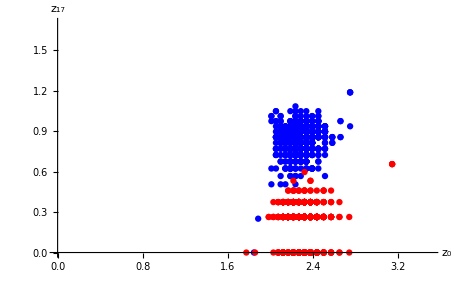

```mathematica
Show[MapThread[ListPlot[Transpose[{arcsin[freqSNPInd[0,#1,chrom]⟦pL⟦pkSNP⟧⟧],arcsin[freqSNPInd[17,#1,chrom]⟦pL⟦pkSNP⟧⟧]}],PlotStyle->{#2,PointSize[0.01]}]&,{{1,2},{Blue,Red}}],PlotRange->{{0,3.5},{0,1.7}},AxesOrigin->{0,0},AxesLabel->{"z_0","z_17"}]
```

This tallies the configurations of numbers seen across these “peak SNP”

```mathematica
pp1=Transpose[{52freqSNPInd[0,1,5]⟦pL⟦pkSNP⟧⟧,64freqSNPInd[17,1,5]⟦pL⟦pkSNP⟧⟧}];
Sort[Tally[pp1]]
```

{{{33,0},1},{{34,1},1},{{37,4},1},{{37,6},1},{{37,14},1},{{37,15},2},{{38,6},1},{{38,8},3},{{38,9},3},{{38,10},1},{{38,11},5},{{38,12},1},{{38,13},1},{{38,14},2},{{38,16},2},{{39,4},1},{{39,5},1},{{39,7},2},{{39,8},1},{{39,9},2},{{39,10},4},{{39,11},9},{{39,12},4},{{39,13},4},{{39,14},2},{{39,15},2},{{40,4},1},{{40,6},4},{{40,7},2},{{40,8},4},{{40,9},8},{{40,10},7},{{40,11},9},{{40,12},14},{{40,13},3},{{41,5},2},{{41,6},8},{{41,7},6},{{41,8},6},{{41,9},15},{{41,10},5},{{41,11},22},{{41,12},7},{{41,13},14},{{41,14},3},{{41,16},1},{{42,4},1},{{42,5},2},{{42,6},3},{{42,7},5},{{42,8},20},{{42,9},22},{{42,10},17},{{42,11},19},{{42,12},21},{{42,13},14},{{42,14},3},{{42,15},3},{{42,16},1},{{42,17},1},{{43,5},1},{{43,6},1},{{43,7},10},{{43,8},12},{{43,9},23},{{43,10},22},{{43,11},23},{{43,12},32},{{43,13},22},{{43,14},6},{{43,15},1},{{43,16},1},{{44,6},3},{{44,7},10},{{44,8},14},{{44,9},23},{{44,10},18},{{44,11},22},{{44,12},24},{{44,13},16},{{44,14},10},{{44,15},1},{{44,16},1},{{45,6},7},{{45,8},5},{{45,9},8},{{45,10},15},{{45,11},18},{{45,12},12},{{45,13},10},{{45,14},4},{{45,15},2},{{46,6},1},{{46,7},2},{{46,8},2},{{46,9},10},{{46,11},16},{{46,12},11},{{46,13},10},{{46,14},5},{{46,15},2},{{46,16},1},{{47,5},1},{{47,8},1},{{47,9},3},{{47,10},2},{{47,11},6},{{47,12},8},{{47,13},5},{{48,10},2},{{48,11},3},{{49,11},2},{{49,14},2},{{50,13},1},{{50,20},3}}

```mathematica
pp2=Transpose[{50freqSNPInd[0,2,5]⟦pL⟦pkSNP⟧⟧,58freqSNPInd[17,2,5]⟦pL⟦pkSNP⟧⟧}];
Sort[Tally[pp2]]
```

{{{30,0},1},{{32,0},1},{{35,1},2},{{36,0},1},{{36,1},3},{{36,2},1},{{37,0},5},{{37,1},6},{{37,2},4},{{38,0},12},{{38,1},17},{{38,2},16},{{39,0},7},{{39,1},47},{{39,2},20},{{39,3},2},{{40,0},21},{{40,1},42},{{40,2},33},{{40,3},4},{{40,4},1},{{41,0},31},{{41,1},74},{{41,2},37},{{41,3},3},{{42,0},26},{{42,1},70},{{42,2},49},{{42,3},4},{{42,5},1},{{43,0},27},{{43,1},65},{{43,2},37},{{43,3},2},{{43,4},2},{{44,0},18},{{44,1},37},{{44,2},13},{{44,3},1},{{45,0},9},{{45,1},19},{{45,2},5},{{45,3},3},{{46,0},5},{{46,1},9},{{46,2},3},{{46,3},1},{{47,0},2},{{47,1},2},{{47,2},1},{{48,0},1},{{48,1},1},{{50,6},3}}

```mathematica
pp12=Transpose[{52freqSNPInd[0,1,5]⟦pL⟦pkSNP⟧⟧+50freqSNPInd[0,2,5]⟦pL⟦pkSNP⟧⟧,64freqSNPInd[17,1,5]⟦pL⟦pkSNP⟧⟧+58freqSNPInd[17,2,5]⟦pL⟦pkSNP⟧⟧}];
Sort[Tally[pp12]]
```

{{{64,1},1},{{65,0},1},{{73,4},1},{{73,9},2},{{74,10},1},{{75,6},1},{{75,8},1},{{75,14},1},{{76,9},1},{{76,13},3},{{76,18},2},{{77,8},1},{{77,9},1},{{77,10},1},{{77,11},1},{{77,12},4},{{77,13},1},{{77,15},1},{{77,16},2},{{77,17},1},{{78,5},1},{{78,8},1},{{78,10},2},{{78,11},2},{{78,12},4},{{78,13},2},{{78,14},1},{{78,15},1},{{78,16},1},{{79,9},1},{{79,10},1},{{79,11},3},{{79,12},4},{{79,13},2},{{79,14},7},{{79,15},1},{{80,4},1},{{80,8},2},{{80,9},1},{{80,10},1},{{80,11},6},{{80,12},11},{{80,13},5},{{80,15},2},{{80,16},1},{{81,4},1},{{81,6},2},{{81,7},7},{{81,8},4},{{81,9},12},{{81,10},6},{{81,11},6},{{81,12},8},{{81,13},6},{{81,14},3},{{81,15},3},{{81,16},1},{{81,17},1},{{82,7},1},{{82,8},4},{{82,9},9},{{82,10},16},{{82,11},6},{{82,12},5},{{82,13},12},{{82,14},10},{{82,15},2},{{82,16},1},{{82,18},1},{{83,7},2},{{83,8},1},{{83,9},3},{{83,10},15},{{83,11},18},{{83,12},12},{{83,13},17},{{83,14},5},{{83,15},5},{{83,16},1},{{83,21},1},{{84,6},2},{{84,7},6},{{84,8},3},{{84,9},7},{{84,10},12},{{84,11},12},{{84,12},7},{{84,13},13},{{84,14},17},{{84,15},4},{{84,16},4},{{84,18},1},{{85,6},1},{{85,7},2},{{85,8},4},{{85,9},8},{{85,10},14},{{85,11},17},{{85,12},20},{{85,13},11},{{85,14},13},{{85,15},12},{{85,17},2},{{86,7},2},{{86,8},7},{{86,9},7},{{86,10},11},{{86,11},14},{{86,12},14},{{86,13},17},{{86,14},10},{{86,15},5},{{86,16},6},{{86,17},2},{{86,18},1},{{87,7},4},{{87,8},3},{{87,9},5},{{87,10},11},{{87,11},9},{{87,12},16},{{87,13},18},{{87,14},5},{{87,15},6},{{87,16},1},{{87,17},2},{{87,18},1},{{88,6},1},{{88,7},2},{{88,8},2},{{88,9},6},{{88,10},6},{{88,11},10},{{88,12},8},{{88,13},8},{{88,14},7},{{88,15},6},{{88,16},4},{{89,6},2},{{89,7},2},{{89,9},2},{{89,10},7},{{89,11},6},{{89,12},6},{{89,13},5},{{89,14},1},{{89,15},2},{{90,8},2},{{90,9},2},{{90,11},4},{{90,13},4},{{90,14},1},{{90,15},4},{{91,10},1},{{91,11},1},{{91,12},5},{{91,13},4},{{91,14},3},{{92,8},1},{{92,11},1},{{92,12},1},{{92,13},2},{{92,14},1},{{92,15},1},{{92,16},1},{{93,13},1},{{93,16},1},{{95,12},1},{{96,15},1},{{100,26},3}}

This is the mean frequency at beginning and end (the mean of the above diagram)

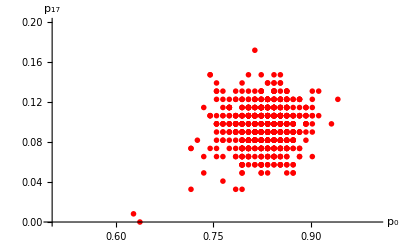

```mathematica
ListPlot[pp12/.{a_,b_}:>{a/102,b/122},PlotStyle->{PointSize[0.01],Red},PlotRange->{{0.5,1},{0,0.2}},AxesLabel->{"p_0","p_17"}]
```

These are the mean allele frequency shifts of the 807 “peak SNP”, and the estimated selection coefficients in the two lines - based on a simple deterministic model.

```mathematica
aa=N[{Mean[pp1]/{52,64},Mean[pp2]/{50,58}}];
{aa,Mean[aa]}
```

{{{0.825183,0.165156},{0.830483,0.0198052}},{0.827833,0.0924808}}

```mathematica
ss=1/17 Log[(#⟦2⟧)/(1-#⟦2⟧)(1-#⟦1⟧)/(#⟦1⟧)]&/@aa;
{ss,Mean[ss]}
```

{{-0.186601,-0.322992},-0.254797}

#### MLE for selection on the chrom. 5 candidate

```mathematica
transitionMatrixFast[20,0.1,0,10^-4]
```

SparseArray[…]

```mathematica
freqSNPInd[0,1,chrom]⟦pL⟧
```

#### Selection within families

Suppose that we have an allele with effect α, scaled relative to V_E=1. Families have a probability 4pq(1-2pq) of segregating  for one heterozygote, in which case the frequency amongst offspring is 1/4 or 3/4, and 4 p^2 q^2 of segregating for both, in which case the frequency is 1/2. Selection on this allele is only effective if the allele segregates.  We need to work out the change in net frequency, after within-family selection, across all 9 classes.

Consider single heterozygotes.  We have in the population two classes, differing in mean by α, and with variance V_E+V_A/2 (since within-family variance is half the total genetic variance with random mating). I ignore the slight excess of heterozygotes due to the mating scheme, since this is O(1/N).  So, we need to find the probability that individuals with mean +α/2 will end up in the top 2/k.  Let the two classes have distribution f_0,f_1; there are k_0,k_1in each class.  Let the cumulative distribution be F_i. The probability that an individual in class 1 comes top and has value z is P_1=k_1 f_1[z]F_1[z]^(k_1-1)F_0[z]^k_0. As a check, if the distributions are identical, this is k_1 f F^(k_1+k_0-1); integrating over z gives k_1/(k_0+k_1).

This integral cannot be solved explicitly, but we can find its derivative wrt a shift ϵ  in the distribution:

(∂P_1)/(∂ϵ)=∫_(-∞)^∞ k_1(f'[z]F[z]-(k_1-1)f[z]^2)F[z]^(k_0+k_1-2)ⅆz

It is more accurate to sum over a binomial distribution of the classes, which yields, for a standard Gaussian:

<(∂P_1)/(∂ϵ)≥np∫_(-∞)^∞ k_1(z F[z]-(n-1)p f[z])f[z]F[z]^(n-2)ⅆz

For n=5, this has value ∂_ϵ log[P_1]=0.581, so that the enrichment is by a factor (1+0.581α).  Thus, choosing the best male out of 5  gives an enrichment by a factor 1+0.581α

We also need to do the same calculation for the double heterozygous class, where there are k_0,k_1,k_2 with distributions f_0,f_1,f_2.  If these are similar, we can use the same calculation to find the chance that any particular class, deviating by a small shift α, will come top.  The probability that class j comes top is just P+α_j P', regardless of how many classes there are, but P’ depends on the frequency of the class.  The contribution of the three classes is {1/4,1/2+α P'_(1/2),1/4+2α P'_(1/4)}. SInce the frequency of the allele within these classes is {0,1/2,1}, the net contribution is 1/2+α(P'_(1/2)+2 P'_(1/4)), or 1/2(1+2α(P'_(1/2)+2 P'_(1/4))).  For 5 individuals, the enrichment is 1.45α.

Overall, then, we have class frequencies, frequencies within classes, and enrichments:

q^4 | 2p q^3 | p^2 q^2
2p q^3 | 4 p^2 q^2 | 2 p^3 q
p^2 q^2 | 2 p^3 q | p^4         0 | 1/4 | 1/2
1/4 | 1/2 | 3/4
1/2 | 3/4 | 1         0 | 2α γ_1 | 0
2α γ_1 | 2α γ_1+4α γ_2 | 2α γ_1
0 | 2α γ_1 | 0

This gives a net selection coefficient 2α ((1+2 p^2) P'_(1/2)+4 pq P'_(1/4)) or  α(3 P'_(1/2)+2 P'_(1/4))= 1.31α for 5 individuals.

```mathematica
Total[{{q^4, 2p q^3, p^2 q^2}, {2p q^3, 4 p^2 q^2, 2 p^3 q}, {p^2 q^2, 2 p^3 q, p^4}} {{0, 1/4, 1/2}, {1/4, 1/2, 3/4}, {1/2, 3/4, 1}} ,2]/.q->1-p//Factor//Simplify
```

p

```mathematica
Total[{{q^4, 2p q^3, p^2 q^2}, {2p q^3, 4 p^2 q^2, 2 p^3 q}, {p^2 q^2, 2 p^3 q, p^4}} {{0, 1/4, 1/2}, {1/4, 1/2, 3/4}, {1/2, 3/4, 1}} {{0, 2a  Subscript[γ, 1], 0}, {2a  Subscript[γ, 1], 2a  Subscript[γ, 1]+4a  Subscript[γ, 2], 2a  Subscript[γ, 1]}, {0, 2a  Subscript[γ, 1], 0}},2]/.q->1-p//Factor//Simplify
```

-2 a (-1+p) p ((1+2 p^2) γ_1-4 (-1+p) p γ_2)

```mathematica
{2dProbSel[5,0.5],2dProbSel[5,0.5]+4dProbSel[5,0.25],3dProbSel[5,0.5]+2dProbSel[5,0.25]}
```

{0.581482,1.45371,1.30834}

```mathematica
2 ((1+2 p^2) Subscript[γ, 1]-4 (-1+p) p Subscript[γ, 2])/.{p->1/2,Subscript[γ, 1]->dProbSel[5,0.5],Subscript[γ, 2]->dProbSel[5,0.25]}
```

1.30834

## Definitions

#### $HistoryLength

This saves memory by not saving In[] and Out[] indefinitely far back.

```mathematica
$HistoryLength=10;
```

#### Pr

```mathematica
Pr::usage="Pr[z] is the integral of a standard normal";
```

```mathematica
Pr[x_]:=1/2 (1+Erf[x/(√2)]);
```

#### probSel

```mathematica
probSel::usage="probSel[{k_0,k_1},ϵ] gives the probability that one of the k_1 individuals in class 1 comes top, given that the two classes have standard normal distributions, with class 1 having a mean ϵ higher. probSel[n,p,ϵ] gives the average, where k_1 is binomially distributed with probability p";
```

```mathematica
probSel[{k0_,k1_},ϵ_]:=Module[{z},NIntegrate[k1((ⅇ^(-(z-ϵ)^2/2))/(√(2π)))Pr[z-ϵ]^(k1-1)Pr[z]^k0,{z,-∞,∞}]];
```

```mathematica
probSel[n_Integer,p_,ϵ_]:=Module[{z},n p NIntegrate[((ⅇ^(-(z-ϵ)^2/2))/(√(2π)))((1-p) Pr[z]+p Pr[z-ϵ])^(n-1),{z,-∞,∞}]];
```

```mathematica
{∑_(k1=1)^5 Binomial[5,k1] 0.4^(5-k1)0.6^k1 probSel[{5-k1,k1},0.01],probSel[5,0.6,0.01]}
```

{0.602789,0.602789}

#### dProbSel

```mathematica
dProbSel::usage="dProbSel[{k_0,k_1}] gives the derivative of probSel wrt ϵ. dProbSel[n,p] gives the sum of this over a binomial distribution";
```

```mathematica
dProbSel[{k0_,k1_}]:=Module[{z},NIntegrate[k1(z Pr[z]-(k1-1)(ⅇ^(-z^2/2))/(√(2π)))Pr[z]^(k0+k1-2)(ⅇ^(-z^2/2))/(√(2π)),{z,-∞,∞}]];
```

```mathematica
dProbSel[n_Integer,p_]:=Module[{z},n p NIntegrate[(z Pr[z]-(n-1)p (ⅇ^(-z^2/2))/(√(2π)) )((ⅇ^(-z^2/2))/(√(2π)))Pr[z]^(n-2),{z,-∞,∞}]];
```

```mathematica
{∑_(k1=1)^4 Binomial[5,k1] 0.4^(5-k1)0.6^k1 dProbSel[{5-k1,k1}],dProbSel[5,0.6]}
```

{0.279111,0.279111}

```mathematica
probSel[{3,7},0]
```

0.7

```mathematica
{(probSel[{3,7},0.001]-0.7)/0.001,dProbSel[{3,7}]}
```

{0.358942,0.359042}

#### winPol

There are now too many window functions...

```mathematica
winPol::usage="winPol[c,10^4,t,r] lists loci in successive 10kb windows, counting within loci that are polymotphic at the specified t, r, as defined for polLoci. winPol[c,10^4,t,r,τ] only includes windows with more than τ SNP.";
```

```mathematica
winPol[c_Integer,k_Integer,t_,r_]:=winPol[c,k,t,r,-1];winPol[c_Integer,k_Integer,t_,r_,τ_]:=winPol[c,k,t,r,τ]=Module[{pL=polLoci[t,r,c]},
Select[GatherBy[Range[Length[pL]],Round[posSNPInd[c]⟦pL⟦#⟧⟧/k]&],Length[#]>τ&]];
```

#### dzPol

I choose not to store dzPol, since it is a much larger structure than dzWinPol

```mathematica
dzPol::usage="dzPol[r,c,t^*,r^*] gives the change in transformed allele frequencies loci in line r, counting only loci that are polymorphic at the specified t^*, r^*, as defined for polLoci. Based on freqSNPInd[]. dzPol[r,𝒫,c,t^*,r^*,method,seed] or dzPol[r,haps,𝒫,c,t^*,r^*,method,seed] does the same, but based on the simulated data in 𝒫.  This uses nThrow[] to throw haplotypes onto a simulation; makeThrow must have been called first to set this up.  The population sizes here are those in the pedigree, which may be larger than those sampled in freqSNPInd[]";
```

```mathematica
dzPol[r:(1|2),c_Integer,tl_,rl_]:=Module[{pL=polLoci[tl,rl,c]},
N[arcsin[freqSNPInd[17,r,c]⟦pL⟧]-arcsin[freqSNPInd[0,r,c]⟦pL⟧]]];
```

```mathematica
dzPol[r:(1|2),𝒫_,c_Integer,tl_,rl_,m_,seed_]:=(*dzPol[r,𝒫,c,tl,rl,m,seed]=*)
Module[{pL=polLoci[tl,rl,c],nt},
nt[t_]:=2.Length[pedigree[r]⟦t+1,1⟧];
arcsin[nThrow[17,r,𝒫,c,tl,rl,m,seed]/nt[17]]-arcsin[nThrow[0,r,𝒫,c,tl,rl,m,seed]/nt[0]]];
```

```mathematica
dzPol[r:(1|2),haps_List,𝒫_,c_Integer,tl_,rl_,m_,seed_]:=(*dzPol[r,𝒫,c,tl,rl,m,seed]=*)
Module[{pL=polLoci[tl,rl,c],nt},
nt[t_]:=2.Length[pedigree[r]⟦t+1,1⟧];
arcsin[nThrow[17,r,haps,𝒫,c,tl,rl,m,seed]/nt[17]]-arcsin[nThrow[0,r,haps,𝒫,c,tl,rl,m,seed]/nt[0]]];
```

#### dzWinPol

```mathematica
dzWinPol::usage="dzWinPol[r,c,j,k,t^*,r^*,τ] stores {x,Δz^j} for line r, counting only loci that are polymorphic at the specified t^*, r^*, in windows defined by winPol[c,k,t^*,r^*,τ]. k is the window size (10^4, say). Based on freqSNPInd[]. dzWinPol[r,𝒫,c,j,k,t^*,r^*,τ,method,seed] or dzWinPol[r,haps,𝒫,c,j,k,t^*,r^*,τ,method,seed] does the same, but based on the simulated data in 𝒫.  This uses nThrow[] to throw haplotypes onto a simulation; makeThrow must have been called first to set this up.";
```

```mathematica
dzWinPol[r:(0|1|2),c_Integer,j_,k_Integer,tl_,rl_]:=dzWinPol[r,c,j,k,tl,rl,-1];
dzWinPol[r:(0|1|2),c_Integer,j_,k_Integer,tl_,rl_,τ_]:=dzWinPol[r,c,j,k,tl,rl,τ]=
Module[{pL=polLoci[tl,rl,c],dzp=dzPol[r,c,tl,rl]},
N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[dzp⟦#⟧^j]}]&/@winPol[c,k,tl,rl,τ]];
```

```mathematica
dzWinPol[r:(0|1|2),𝒫_,c_Integer,j_,k_Integer,tl_,rl_,m_,seed_]:=dzWinPol[r,𝒫,c,j,k,tl,rl,-1,m,seed];
dzWinPol[r:(0|1|2),𝒫_,c_Integer,j_,k_Integer,tl_,rl_,τ_,m_,seed_]:=dzWinPol[r,𝒫,c,j,k,tl,rl,τ,m,seed]=
Module[{pL=polLoci[tl,rl,c],dzp=dzPol[r,𝒫,c,tl,rl,m,seed]},
N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[dzp⟦#⟧^j]}]&/@winPol[c,k,tl,rl,τ]];
```

```mathematica
dzWinPol[r:(0|1|2),haps_List,𝒫_,c_Integer,j_,k_Integer,tl_,rl_,m_,seed_]:=dzWinPol[r,haps,𝒫,c,j,k,tl,rl,-1,m,seed];
dzWinPol[r:(0|1|2),haps_List,𝒫_,c_Integer,j_,k_Integer,tl_,rl_,τ_,m_,seed_]:=
dzWinPol[r,haps,𝒫,c,j,k,tl,rl,τ,m,seed]=
Module[{pL=polLoci[tl,rl,c],dzp=dzPol[r,haps,𝒫,c,tl,rl,m,seed]},
N[{Mean[posSNPInd[chrom]⟦pL⟦#⟧,2⟧],Mean[dzp⟦#⟧^j]}]&/@winPol[c,k,tl,rl,τ]];
```

#### makeFounders

```mathematica
makeFounders::usage="makeFounders[r,c,t^*,r^*,method] uses makeHap to generate a random founder population of haplotypes, based on loci polymorphic in lines t^*,r^*, and with the initial numbers in the pedigree";
```

```mathematica
makeFounders[r:(1|2),c_Integer,tl_,rl_,m_]:=Module[{n0=Length[pedigree[r]⟦1,1⟧]},
RandomSample[makeHaps[dipInd[0,r,c]⟦All,polLoci[tl,rl,c]⟧,2n0,Method->m]]];
```

#### n0Obs

```mathematica
n0Obs::usage="n0Obs[r,c,t^*,r^*] stores the observed initial numbers, based on the polymorphic loci specified by t^*,r^*";
```

```mathematica
n0Obs[r_,c_,tl_,rl_]:=n0Obs[r,c,tl,rl]=Total[dipInd[0,r,c]⟦All,polLoci[tl,rl,c]⟧];
```

#### nThrow

```mathematica
nThrowUsage="nThrow[t,r,𝒫,c,t^*,r^*,method,seed] stores the initial and final numbers, based on a throw of SNP from a single founder population onto the simulation 𝒫. The founder population is specified by seed.  This is set up by makeThrow[𝒫,c,t^*,r^*,method,seed]. The simulation 𝒫 should correspond to the chosen line, r. nThrow[t,r,haps,𝒫,c,t^*,r^*,method,seed] uses a specified set of haplotypes, shuffled according to the seed.";
```

#### makeThrow

Note:
	- A single set of founder haplotypes is used for LS1, LS2, which must initially be the same size
	- throwP[] throws down SNP onto loci in polLoci[t^*,r^*,c] - I am trying to be consistent in using  this throughout; one might perhaps want to restrict to loci polymorphic at the beginning or the end (say).  Thus, I need to rewrite throwP and intSNP
	- nThrow must be called using the correct simulation from the pair.
	- There are some subtleties here.  Each time makeThrow is called with a given seed, it stores a new set of nThrow values, replacing previous ones that used that seed.

```mathematica
makeThrow::usage="makeThrow[{𝒫_1,𝒫_2},c,t^*,r^*,method,seed] uses makeFounders[] to generate a set of founder haplotypes, and uses these to store the initial and final numbers in nThrow, for the two lines.  This avoids storing the full set of haplotypes, which would use too much memory: only the total numbers are stored. Uses haplotypes from LS1, assuming that LS1 and LS2 pedigrees start at the same size. Clear[nThrow] can be used to save memory if necessary. makeThrow[haps,{𝒫_1,𝒫_2},c,t^*,r^*,method,seed] does the same, but by shuffling a specified set of founders.  This is much more efficient in time. Note that here, method is purely used as a flag to label nThrow entries.";
```

```mathematica
makeThrow[𝒫:{_,_},c_,tl_,rl_,m_,seed_]:=Module[{h=makeFounders[1,c,tl,rl,m]},
nThrow::usage=nThrowUsage;
(nThrow[0,#,𝒫⟦#⟧,c,tl,rl,m,seed]=Total[h])&/@{1,2};
(nThrow[17,#,𝒫⟦#⟧,c,tl,rl,m,seed]=throwP[𝒫⟦#⟧,h,17,tl,rl,c])&/@{1,2}];
```

```mathematica
makeThrow[h_List,𝒫:{_,_},c_,tl_,rl_,m_,seed_]:=Module[{hs=RandomSample[h]},
nThrow::usage=nThrowUsage;
(nThrow[0,#,h,𝒫⟦#⟧,c,tl,rl,m,seed]=Total[hs])&/@{1,2};
(nThrow[17,#,h,𝒫⟦#⟧,c,tl,rl,m,seed]=throwP[𝒫⟦#⟧,hs,17,tl,rl,c])&/@{1,2}];
```